# Tree level analysis

We set the assumptions for the variables we are using.

```mathematica
$Assumptions=(And@@(Element[#,Reals]&/@{ϕ,σ,χ,χh}))&&(And@@(Element[#,PositiveReals]&/@{L,Lh,α,r,g,λ,go,Lo,Lho,rp,rm}))&&(And@@(Element[#,Integers]&/@{n5,n5h,n1}));
```

We define the potentials

```mathematica
vol[ϕ_,σ_,χ_,χh_]:=Exp[-2ϕ+σ+3χ+3χh];
intpotential[ϕ_,σ_,χ_,χh_]:=vol[ϕ,σ,χ,χh]^(-2)((2 (α n5)^2)/L^6 Exp[-6 χ]-6/L^2 Exp[-2 χ]+(2 (α n5h)^2)/Lh^6 Exp[-6 χh]-6/Lh^2 Exp[-2 χh]);
AdS3potential[ϕ_,σ_,χ_,χh_]:=vol[ϕ,σ,χ,χh]^(-4) ((8π α^3 g^2)^2)/(2 r^2 L^6 Lh^6)n1^2;
treepotential[ϕ_,σ_,χ_,χh_]:=intpotential[ϕ,σ,χ,χh]+AdS3potential[ϕ,σ,χ,χh];
```

We want the gradient of the potential to be zero for us to be at the minimum.

```mathematica
potentialgradient=D[treepotential[ϕ,0,χ,χh],#]&/@{ϕ,χ,χh}/.{ϕ->0,σ->0,χ->0,χh->0};
treesolutions= {L^2,Lh^2,g^4}/.Solve[potentialgradient==0,{L,Lh,g}]//DeleteDuplicates
```

{{n5 α,n5h α,(n5^2 n5h^2 (n5+n5h) r^2)/(16 n1^2 π^2 α)},{n5 α,-n5h α,(n5^2 (n5-n5h) n5h^2 r^2)/(16 n1^2 π^2 α)},{-n5 α,n5h α,-(n5^2 (n5-n5h) n5h^2 r^2)/(16 n1^2 π^2 α)},{-n5 α,-n5h α,-(n5^2 n5h^2 (n5+n5h) r^2)/(16 n1^2 π^2 α)}}

We are solving for positive L^2,Lh^2,g^4 that make the gradient of the potential zero. This forces us to choose the corresponding solution depending on the sign of n5 and n52. In other words, the solution can be written in terms of the absolute values as the following.

```mathematica
abstreesolutions={
L-> Sqrt[Abs[n5] α], 
Lh -> Sqrt[Abs[n5h] α],
g-> ((n5^2 n5h^2 (Abs[n5]+Abs[n5h]) r^2)/(16 π^2 n1^2 α))^(1/4)
};
```

Indeed the potential has a minimum at ϕ = χ = χh = 0 for these values. We check that each component of the gradient is zero:

```mathematica
#==0&/@(potentialgradient/.abstreesolutions/.r->α^1/2)//Refine
```

{True,True,True}

The minimum of the potential is:

```mathematica
Vmin=(treepotential[0,0,0,0]/.abstreesolutions/.r->α^1/2)//FullSimplify//Expand
```

-2/(α Abs[n5])-2/(α Abs[n5h])

The cosmological constant is

```mathematica
Λtree=Vmin/2//Expand
```

-1/(α Abs[n5])-1/(α Abs[n5h])

# One loop analysis

## Paritition Function

### Modular function definitions

```mathematica
Theta[a_,b_,N_]:=If[Abs[a]==1/2&&Abs[b]==1/2,0,Sum[Exp[2π I (n+a)b]*q^((n+a)^2/2),{n,-N,N}]];
BarTheta[a_,b_,N_]:=If[Abs[a]==1/2&&Abs[b]==1/2,0,Sum[Exp[-2π I (n+a)b]*p^((n+a)^2/2),{n,-N,N}]];
Eta[N_]:=q^(1/24)Product[1-q^n,{n,1,N}];
BarEta[N_]:=p^(1/24)Product[1-p^n,{n,1,N}];
```

### Partial traces

In the definition of partial traces, r is the radius in terms of α’ units, and m is the depth of the lattice sum.

```mathematica
Z11[r_,m_]:=Normal@Series[q^(1)p^(1/2)(1/2)Eta[m]^(-24)BarEta[m]^(-12)(BarTheta[0,0,m]^4-BarTheta[0,1/2,m]^4-BarTheta[1/2,0,m]^4- BarTheta[1/2,1/2,m]^4)(Sum[q^(1/4(n+w)^2)p^(1/4(n-w)^2),{n,-m,m},{w,-m,m}]+480 q Sum[q^(1/4(n+w)^2)p^(1/4(n-w)^2),{n,-3,3},{w,-3,3}]),{q,0,m},{p,0,m}];
Z1g[r_,m_]:=Normal@Series[(1/2)Eta[m]^(-24)BarEta[m]^(-12)(-BarTheta[0,0,m]^4+BarTheta[0,1/2,m]^4+(-1) BarTheta[1/2,0,m]^4- BarTheta[1/2,1/2,m]^4)(Sum[q^(1/4(n/r+w r)^2)p^(1/4(n/r-w r)^2),{n,-m,m},{w,-m,m}]
+2 (112 q+64 E^(2π I/2)q +64 E^(-2π I/2)q )
 Sum[q^(1/4(n/r+w r)^2)p^(1/4(n/r-w r)^2),{n,-3,3},{w,-3,3}]),{q,0,m},{p,0,m}];
Zg1[r_,m_]:=Normal@Series[(1/2)Eta[m]^(-24)BarEta[m]^(-12)(BarTheta[-1/2,0,m]^4-BarTheta[0,0,m]^4+(-1) BarTheta[0,1/2,m]^4- BarTheta[-1/2,1/2,m]^4)(q Sum[q^(1/4(n/r+w r)^2)p^(1/4(n/r-w r)^2),{n,-m,m},{w,-m,m}]
+(2 (14q^(1)+64 q^(3/2) )+14*14 q)
 Sum[q^(1/4(n/r+w r)^2)p^(1/4(n/r-w r)^2),{n,-m,m},{w,-m,m}]),{q,0,m},{p,0,m}];
Zgg[r_,m_]:=Normal@Series[(1/2)Eta[m]^(-24)BarEta[m]^(-12)(BarTheta[-1/2,-1,m]^4+BarTheta[0,-1/2,m]^4-(-1) BarTheta[0,0,m]^4- BarTheta[-1/2,-1/2,m]^4)(q^(1) Sum[q^(1/4(n/r+w r)^2)p^(1/4(n/r-w r)^2),{n,-m,m},{w,-m,m}]
+(2 (14q^(1)-64 q^(3/2) )+14*14 q)
 Sum[q^(1/4(n/r+w r)^2)p^(1/4(n/r-w r)^2),{n,-m,m},{w,-m,m}]),{q,0,m},{p,0,m}];
Ztot[r_,m_]:=1/2(Z1g[r,m]+Zg1[r,m]+Zgg[r,m]);
Zmatched[r_,m_]:=Total[Select[{Coefficient[#,T,Exponent[#,T]],#,Exponent[#,T]}&/@(List@@Expand[Simplify[Ztot[r,m]/.{q-> q T,p-> p/T},T>0]]),#[[3]]==0 &]][[1]];
```

Since we start with a supersymmetric theory, the Z11 partition function should vanish:

```mathematica
Z11[r,3]
```

0

To compute the cosmological constant, we define

```mathematica
CosmConst[r_,m_]:=Re@NIntegrate[Boole[x^2+y^2>1] 1/(2(2π)^9)*1/(y^(11/2))PowerExpand[(Ztot[r,m]//Expand)/.{q-> E^(2 π I (x+ I y)),p-> E^(-2 π I (x- I y))}//Expand],{x,-1/2,1/2},{y,0,1}]+Re@NIntegrate[1/(2(2π)^9)*1/(y^(11/2))PowerExpand[(Zmatched[r,m]//Expand)/.{q-> E^(2 π I (x+ I y)),p-> E^(-2 π I (x- I y))}//Expand],{x,-1/2,1/2},{y,1,20}]
```

```mathematica
potplotvals1=Table[
{r,CosmConst[r,1]}
,{r,{1,4/3,3/2,5/3,2,7/3,5/2,8/3,3,10/3,7/2,11/3,4}}]
```

{{1,0.0000229912},{4/3,0.0000263189},{3/2,0.0000291293},{5/3,0.0000320449},{2,0.0000375144},{7/3,0.000042162},{5/2,0.0000441716},{8/3,0.0000459927},{3,0.0000491452},{10/3,0.0000517617},{7/2,0.0000529059},{11/3,0.0000539569},{4,0.0000558172}}

```mathematica
potplotvals=Join[({#[[1]],#[[2]]}={#[[1]]^(-1),#[[2]]})&/@Reverse[potplotvals1[[2;;-1]]],potplotvals1];
```

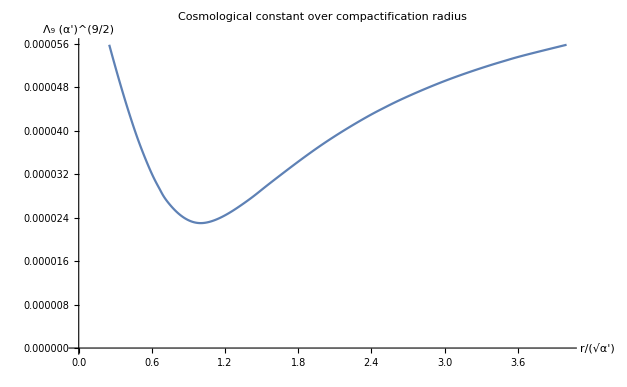

```mathematica
ListPlot[potplotvals,Joined->True,InterpolationOrder->3];
Show[%,AxesLabel->{HoldForm[r/Sqrt[α']],HoldForm[Subscript[Λ, 9] α'^(9/2)]},PlotLabel->HoldForm["Cosmological constant over compactification radius"],LabelStyle->{9,GrayLevel[0]}]
```

## Exact solution for L_o and (L̂)_o

The correction term was computed as

```mathematica
correctionpotential[ϕ_,σ_,χ_,χh_]:=vol[ϕ,σ,χ,χh]^(-3)Exp[3χ+3χh] 2 λ go^2/α;
```

The total one - loop potential is

```mathematica
onelooppotential[ϕ_,σ_,χ_,χh_]:=(treepotential[ϕ,σ,χ,χh]/.{L->Lo,Lh-> Lho,g->go})+correctionpotential[ϕ,σ,χ,χh];
```

We again want the gradient of the potential to vanish at ϕ = χ = χh = 0. We first solve for L_o and (L̂)_o using linear combinations of the components of the gradient.

```mathematica
gradcomp1=Lo^6/12(3 D[#,ϕ]+2 D[#,χ])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0}//Expand//Simplify
gradcomp2=Lho^6/12(3 D[#,ϕ]+2 D[#,χh])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0}//Expand//Simplify
```

2 Lo^4-2 n5^2 α^2+(go^2 Lo^6 λ)/α

2 Lho^4-2 n5h^2 α^2+(go^2 Lho^6 λ)/α

Solving for L_o^2 and  ((L̂)_o)^2:

```mathematica
loopsolns=Solve[{gradcomp1==0,gradcomp2==0},{Lo,Lho}][[1]]//Expand
```

{Lo→-1/(√3)(√(-(2 α)/(go^2 λ)+(4 α^2)/(go^2 λ (-8 α^3+27 go^4 n5^2 α^3 λ^2+3 √3 √(go^4 n5^2 α^6 λ^2 (-16+27 go^4 n5^2 λ^2)))^(1/3))+((-8 α^3+27 go^4 n5^2 α^3 λ^2+3 √3 √(go^4 n5^2 α^6 λ^2 (-16+27 go^4 n5^2 λ^2)))^(1/3))/(go^2 λ))),Lho→-1/(√3)(√(-(2 α)/(go^2 λ)+(4 α^2)/(go^2 λ (-8 α^3+27 go^4 n5h^2 α^3 λ^2+3 √3 √(go^4 n5h^2 α^6 λ^2 (-16+27 go^4 n5h^2 λ^2)))^(1/3))+((-8 α^3+27 go^4 n5h^2 α^3 λ^2+3 √3 √(go^4 n5h^2 α^6 λ^2 (-16+27 go^4 n5h^2 λ^2)))^(1/3))/(go^2 λ)))}

## Small g_s^2 limit

Taking the small (g_(s,o))^2 limit, we get

```mathematica
smallloopsolns=Normal@Series[{Lo^2,Lho^2}/.loopsolns,{go,0,2}]//Refine//Simplify
```

{-1/4 go^2 n5^2 α λ+α Abs[n5],-1/4 go^2 n5h^2 α λ+α Abs[n5h]}

We can' t have a closed-form expression for (g_(s,o))^2. Instead, we solve for it in the small g_s^2 limit.

```mathematica
gradcomp3a=Expand@D[onelooppotential[ϕ,σ,χ,χh],ϕ]/.{ϕ->0,σ->0,χ->0,χh->0}/.{Lo-> Sqrt@smallloopsolns[[1]],Lho-> Sqrt@smallloopsolns[[2]]}/.n1-> (Abs[n5]Abs[n5h]Sqrt[Abs[n5]+Abs[n5h]]r)/(4 π Sqrt[α]g^2)/.r->Sqrt[α]/.g->go/cc^(1/4);
gradcomp3=Normal@Series[Normal@Series[gradcomp3a,{go,0,6},{cc,0,2}]/.cc->go^4/g^4,{go,0,6}];
smallg2loop=Normal@Series[go^2/.Solve[gradcomp3==0,go][[1]],{g,0,4}];
```

$Aborted

```mathematica
(Normal@Series[g^2(1-3/8 λ(Abs[n5]+Abs[n5h]+Abs[n5 n5h]/(Abs[n5]+Abs[n5h]))g^2)-smallg2loop,{g,0,4}]//Simplify//FullSimplify)==0
```

True

```mathematica
smallg2loop=g^2(1-3/8 λ(Abs[n5]+Abs[n5h]+Abs[n5 n5h]/(Abs[n5]+Abs[n5h]))g^2);
```

Minimum of the potential in the small g_s^2 limit is then

```mathematica
Vminsmallg=Normal@Series[onelooppotential[0,0,0,0]/.{Lo-> Sqrt@smallloopsolns[[1]],Lho-> Sqrt@smallloopsolns[[2]]}/.go->Sqrt@smallg2loop/.n1-> Abs[n5 n5h] Sqrt[Abs[n5]+Abs[n5h]]r/(4π Sqrt[α] g^2)/.r->Sqrt[α],{g,0,2}]//Expand//FullSimplify//Expand
```

(g^2 λ)/(2 α)-2/(α Abs[n5])-2/(α Abs[n5h])

The one loop corrected cosmological constant is

```mathematica
Λloopsmallg=Vminsmallg/2//Expand
```

(g^2 λ)/(4 α)-1/(α Abs[n5])-1/(α Abs[n5h])

We can show that uplifting to de Sitter is impossible in the small g_s^2 regime:

```mathematica
Reduce[Λloopsmallg>0&&λ Abs[n5] g^2<1&&λ Abs[n5h] g^2<1]//Simplify
```

False

## Numerical analysis

We will do numerical computations in this section since closed-form solutions are not possible.

```mathematica
ccval=λ->(0.000022917283122037653)* (2π)^6/2
lambdasub=Λloop->( onelooppotential[0,0,0,0]/2/.r->Sqrt@α/.α->1/.ccval);
```

λ→0.705038

Choose the values of n5, n5h, n1 you want to plot over.

```mathematica
n5vals={500,1000,5000,10000};
n5hvals={500,1000};
n5tuples=Tuples[{n5vals,n5hvals}];
n1vals=Table[10^(n/2),{n,10,30}];
```

Alternatively, choose n5, n5h as

```mathematica
n5tuples={{500,500},{1000,500},{500,1000},{1000,1000},{2000,1000},{5000,1000},{10000,1000}};
```

Choose the variables to plot

```mathematica
vars={Lo,Lho,go,Λloop};
```

Running the following code produces the graphs for the variables.

```mathematica
varlen=Length@vars;
plotvals=Table[{},varlen];
Monitor[
For[n5tuplesind=1,n5tuplesind≤ Length@n5tuples,n5tuplesind++,
AppendTo[plotvals[[#]],{}]&/@Array[#1&,varlen];
For[n1ind=1,n1ind≤ Length@n1vals,n1ind++,

thesolutions=NSolve[(D[onelooppotential[ϕ,σ,χ,χh],#]/.{ϕ->0,σ->0,χ->0,χh->0}/.r->Sqrt[α]/.α->1/.ccval/.{n5->n5tuples[[n5tuplesind,1]],n5h->n5tuples[[n5tuplesind,2]],n1->n1vals[[n1ind]]+1.2})==0&/@{ϕ,χ,χh},PositiveReals];

solns[n5tuplesind,n1ind]=vars/.lambdasub/.thesolutions[[-1]]/.{n5->n5tuples[[n5tuplesind,1]],n5h->n5tuples[[n5tuplesind,2]],n1->n1vals[[n1ind]]+1.2}/.ccval;

If[
Length@thesolutions==0,
If[
n1ind==1,
solns[n5tuplesind,n1ind]=solns[n5tuplesind,n1ind+1]/.ccval,
If[
n1ind==Length@n1vals,
solns[n5tuplesind,n1ind]=solns[n5tuplesind,n1ind-1]/.ccval,solns[n5tuplesind,n1ind]=(solns[n5tuplesind,n1ind-1]+solns[n5tuplesind,n1ind+1])*0.5/.ccval
]
]
];
AppendTo[plotvals[[#,n5tuplesind]],solns[n5tuplesind,n1ind][[#]]]&/@Array[#1&,varlen];
]
]
,{"n5="<>ToString@n5tuples[[n5tuplesind,1]],"n5h="<>ToString@n5tuples[[n5tuplesind,2]],"n1="<>ToString@IntegerPart@n1vals[[n1ind]]}]
```

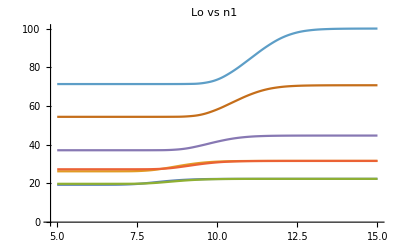
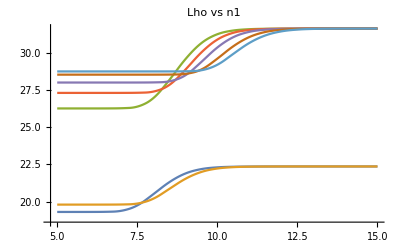
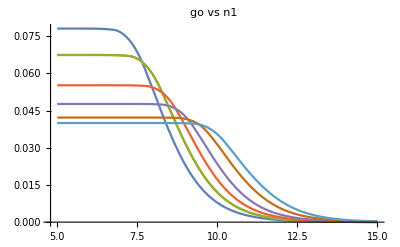
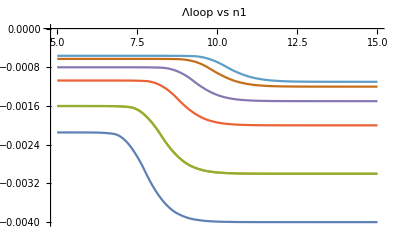

```mathematica
plotslist=ListPlot[Table[{(n1ind-1)/2+5,plotvals[[#,n5tuplesind,n1ind]]},{n5tuplesind,1,Length@n5tuples},{n1ind,1,Length@n1vals}],Joined->True,InterpolationOrder->2,PlotLabel->ToString[vars[[#]]]<>" vs n1"]&/@Array[#1&,varlen]
```

#### Plots with Legends

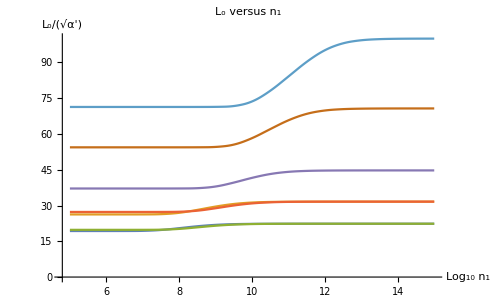

```mathematica
Show[plotslist[[1]],AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 1]],HoldForm[Subscript[L, o]/(√α')]},PlotLabel->Style[HoldForm["L_o versus n_1"],FontSize->18],LabelStyle->{15,GrayLevel[0]}]
```

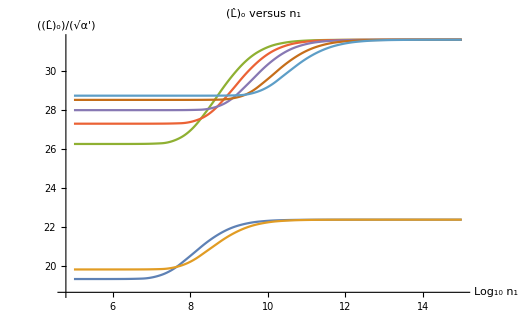

```mathematica
Show[plotslist[[2]],AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 1]],HoldForm[Subscript[L̂, o]/(√α')]},PlotLabel->HoldForm[Subscript[L̂, o] versus Subscript[n, 1]],LabelStyle->{15,GrayLevel[0]}]
```

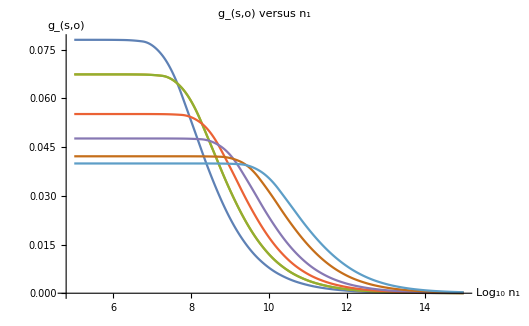

```mathematica
Show[plotslist[[3]],AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 1]],HoldForm[Subscript[g, s,o]]},PlotLabel->HoldForm[Subscript[g, s,o] versus Subscript[n, 1]],LabelStyle->{15,GrayLevel[0]}]
```

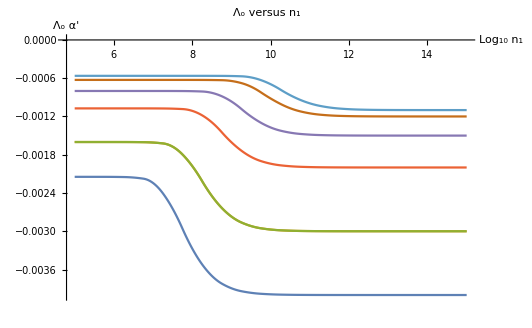

```mathematica
Show[plotslist[[4]],AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 1]],HoldForm[Subscript[Λ, o] α']},PlotLabel->HoldForm[Subscript[Λ, o] versus Subscript[n, 1]],LabelStyle->{15,GrayLevel[0]}]
```

```mathematica
ListPlot[plotvals[[1,1;;Length@n5tuples]],Joined->True,PlotLegends->Automatic]
```

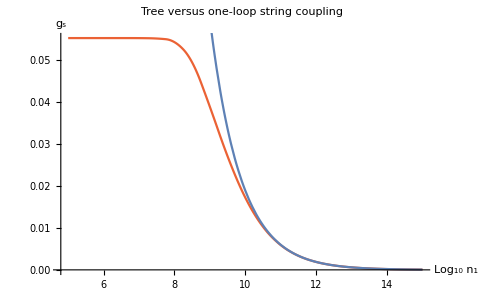

```mathematica
Show[ListPlot[
Table[{(n1-1)/2+5,plotvals[[3,4,n1]]},{n1,1,21}],Joined->True,InterpolationOrder->2,PlotStyle-> ColorData[97,"ColorList"][[4]]],Plot[Sqrt[1000 1000 Sqrt[2000]/(4π 10^n1)],{n1,5,15}]];
Show[%,AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 1]],HoldForm[Subscript[g, s]]},PlotLabel->HoldForm["Tree versus one-loop string coupling"],LabelStyle->{15,GrayLevel[0]}]LineLegend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[4]]},{"g_s","g_(s, o)"}]
```

# Spectrum Analysis

The following Mathematica code is taken from the ancillary file of arXiv:1701.03552. We denote where our modifications to their code are.

## Definition of Manifolds, Tensors and Replacement rules

```mathematica
<<xAct`xPert`
<<xAct`xTras`
DefManifold[AdS3,3,{μ,ν,λ,ρ,σ,τ}]
DefManifold[S3p,3,{a,b,c,d,e,f}]
DefManifold[S3m,3,{i,j,k,l,m,n}]
DefManifold[AdS3S3S3,{AdS3,S3p,S3m},{M,P,Q,R,T}]
DefMetric[-1,gAdS3[-μ,-ν],CDAdS3,SymbolOfCovD->{";","∇"}]
DefMetric[1,gS3p[-a,-b],CDS3p,SymbolOfCovD->{";","∇"}]
DefMetric[1,gS3m[-i,-j],CDS3m,SymbolOfCovD->{";","∇"}]
SetOptions[ContractMetric,OverDerivatives->True]
DefConstantSymbol[ℓ]
DefConstantSymbol[rp]
DefConstantSymbol[rm]
(*begin modification*)
DefConstantSymbol[Λ]
DefConstantSymbol[go]
(*end of modification*)
DefProductMetric[g[-M,-P],{{TangentAdS3,1},{TangentS3p,1},{TangentS3m,1}},CD,SymbolOfCovD->{";","∇"}]
DefTensor[H[-M,-P,-R],AdS3S3S3,Antisymmetric[{-M,-P,-R}]]
DefTensor[Φ[],AdS3S3S3]
DefTensor[Ψ[],AdS3S3S3]
DefTensor[A1[-M],AdS3S3S3]
DefTensor[A2[-M],AdS3S3S3]
(*begin modification*)
DefTensor[φ[],AdS3S3S3]
DefTensor[dφ[],AdS3S3S3]
DefTensor[A3[-M],AdS3S3S3]
DefTensor[F3[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}],PrintAs->"𝔉"]
DefTensor[Z3[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}],PrintAs->"ℨ"]
DefTensorPerturbation[φφ[LI[order]],φ[],AdS3S3S3]
DefTensorPerturbation[F3pert[LI[order],-M,-P],F3[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}]]
DefTensorPerturbation[A3pert[LI[order],-M],A3[-M],AdS3S3S3]
Unprotect[IndexForm];
(*end modification*)
DefTensor[F1[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}],PrintAs->"F"]
DefTensor[F2[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}],PrintAs->"F̂"]
DefTensor[B[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}]]
DefTensor[r[-M,-P],AdS3S3S3,Symmetric[{-M,-P}],PrintAs->"h"]
DefTensor[X[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}]]
DefTensor[Z1[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}],PrintAs->"Z"]
DefTensor[Z2[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}],PrintAs->"Ẑ"]
DefTensor[Ξ[-M,-P,-R],AdS3S3S3,Antisymmetric[{-M,-P,-R}]]
DefTensor[Y1[-M],AdS3S3S3]
DefTensor[Y2[-M],AdS3S3S3]
DefTensor[ϕ[],AdS3S3S3]
DefTensor[ψ[],AdS3S3S3]
DefTensor[H2[-μ,-ν],AdS3S3S3,Symmetric[{-μ,-ν}],PrintAs->"H"]
DefTensor[K[-a,-b],AdS3S3S3,Symmetric[{-a,-b}]]
DefTensor[L[-i,-j],AdS3S3S3,Symmetric[{-i,-j}]]
DefTensor[M0[],AdS3S3S3,PrintAs->"M"]
DefTensor[N0[],AdS3S3S3,PrintAs->"N"]
DefTensor[P0[],AdS3S3S3,PrintAs->"P"]
DefTensor[U[-μ],AdS3S3S3]
DefTensor[V[-a],AdS3S3S3]
DefTensor[W[-b],AdS3S3S3]
DefTensor[R0[-μ,-a],AdS3S3S3,PrintAs->"R"]
DefTensor[S0[-μ,-i],AdS3S3S3,PrintAs->"S"]
DefTensor[T0[-a,-i],AdS3S3S3,PrintAs->"T"]
DefTensor[C0[-μ,-a],AdS3S3S3,PrintAs->"C"]
DefTensor[D0[-μ,-i],AdS3S3S3,PrintAs->"D"]
DefTensor[E0[-a,-i],AdS3S3S3,PrintAs->"E"]
DefMetricPerturbation[g,h,ϵ]
DefTensorPerturbation[Bpert[LI[order],-M,-P],B[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}]]
DefTensorPerturbation[Hpert[LI[order],-M,-P,-R],H[-M,-P,-R],AdS3S3S3,Antisymmetric[{-M,-P,-R}]]
DefTensorPerturbation[ϕϕ[LI[order]],Φ[],AdS3S3S3]
DefTensorPerturbation[ψψ[LI[order]],Ψ[],AdS3S3S3]
DefTensorPerturbation[F1pert[LI[order],-M,-P],F1[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}]]
DefTensorPerturbation[F2pert[LI[order],-M,-P],F2[-M,-P],AdS3S3S3,Antisymmetric[{-M,-P}]]
DefTensorPerturbation[A1pert[LI[order],-M],A1[-M],AdS3S3S3]
DefTensorPerturbation[A2pert[LI[order],-M],A2[-M],AdS3S3S3]
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical]
(*begin modification*)
(*Relation between S3 radii and AdS3 radius*)
ℓ=(rp^-2+rm^-2-3/4 Λ)^(-1/2); 
(*end modification*)
(*Implement the rules for the Riemann Curvature Tensor*)
AdSrules = SymmetricSpaceRules[CDAdS3,-ℓ^-2];
S3prules = SymmetricSpaceRules[CDS3p,rp^-2];
S3mrules = SymmetricSpaceRules[CDS3m,rm^-2];
(*Redefine perturbations as nice tensors*)
replacementpert=Flatten[Map[MakeRule[#]&,{{{{h, {{1, R, P}, {, , }}}},r[R,P]},{{{h, {{2, M, P}, {, , }}}},0},{{{F1pert, {{1, M, P}, {, , }}}},Z1[M,P]},{{{F1pert, {{2, , }, {, M, P}}}},0},{{{F2pert, {{1, , }, {, M, P}}}},Z2[-M,-P]},{{{F2pert, {{2, , }, {, M, P}}}},0},
(*begin modification*)
{{{F3pert, {{1, , }, {, M, P}}}},Z3[-M,-P]},{{{F3pert, {{2, , }, {, M, P}}}},0},{{{φφ, {{1}, {}}}},dφ[]},{{{φφ, {{2}, {}}}},0},
(*end modification*)
{{{ϕϕ, {{1}, {}}}},ϕ[]},{{{ϕϕ, {{2}, {}}}},0},{{{ψψ, {{1}, {}}}},ψ[]},{{{ψψ, {{2}, {}}}},0},{{{Hpert, {{1, , , }, {, P, R, Q}}}},Ξ[-P,-R,-Q]},{{{Hpert, {{2, , , }, {, M, P, R}}}},0}}]];
(*Replace the 3-form field strength by its potential*)
potentialpert=Flatten[Map[MakeRule[#]&,{{Ξ[-M,-P,-Q],CD[-M]@X[-P,-Q]+CD[-P]@X[-Q,-M]+CD[-Q]@X[-M,-P]},{Ξ[-μ,-ν,-λ],CDAdS3[-μ]@X[-ν,-λ]+CDAdS3[-ν]@X[-λ,-μ]+CDAdS3[-λ]@X[-μ,-ν]},{Ξ[-a,-b,-c],CDS3p[-a]@X[-b,-c]+CDS3p[-b]@X[-c,-a]+CDS3p[-c]@X[-a,-b]},{Ξ[-i,-j,-k],CDS3m[-i]@X[-j,-k]+CDS3m[-j]@X[-k,-i]+CDS3m[-k]@X[-i,-j]},{Ξ[-μ,-ν,-a],CDAdS3[-μ]@X[-ν,-a]+CDAdS3[-ν]@X[-a,-μ]+CDS3p[-a]@X[-μ,-ν]},{Ξ[-a,-μ,-ν],CDAdS3[-μ]@X[-ν,-a]+CDAdS3[-ν]@X[-a,-μ]+CDS3p[-a]@X[-μ,-ν]},{Ξ[-μ,-a,-ν],-CDAdS3[-μ]@X[-ν,-a]-CDAdS3[-ν]@X[-a,-μ]-CDS3p[-a]@X[-μ,-ν]},{Ξ[-μ,-b,-a],CDAdS3[-μ]@X[-b,-a]+CDS3p[-b]@X[-a,-μ]+CDS3p[-a]@X[-μ,-b]},{Ξ[-b,-μ,-a],-CDAdS3[-μ]@X[-b,-a]-CDS3p[-b]@X[-a,-μ]-CDS3p[-a]@X[-μ,-b]},{Ξ[-b,-a,-μ],CDAdS3[-μ]@X[-b,-a]+CDS3p[-b]@X[-a,-μ]+CDS3p[-a]@X[-μ,-b]},{Ξ[-μ,-i,-a],CDAdS3[-μ]@X[-i,-a]+CDS3m[-i]@X[-a,-μ]+CDS3p[-a]@X[-μ,-i]},{Ξ[-μ,-a,-i],-CDAdS3[-μ]@X[-i,-a]-CDS3m[-i]@X[-a,-μ]-CDS3p[-a]@X[-μ,-i]},{Ξ[-i,-μ,-a],-CDAdS3[-μ]@X[-i,-a]-CDS3m[-i]@X[-a,-μ]-CDS3p[-a]@X[-μ,-i]},{Ξ[-a,-μ,-i],CDAdS3[-μ]@X[-i,-a]+CDS3m[-i]@X[-a,-μ]+CDS3p[-a]@X[-μ,-i]},{Ξ[-i,-a,-μ],CDAdS3[-μ]@X[-i,-a]+CDS3m[-i]@X[-a,-μ]+CDS3p[-a]@X[-μ,-i]},{Ξ[-a,-i,-μ],-CDAdS3[-μ]@X[-i,-a]-CDS3m[-i]@X[-a,-μ]-CDS3p[-a]@X[-μ,-i]},{Ξ[-μ,-i,-ν],CDAdS3[-μ]@X[-i,-ν]+CDS3m[-i]@X[-ν,-μ]+CDAdS3[-ν]@X[-μ,-i]},{Ξ[-μ,-ν,-i],-CDAdS3[-μ]@X[-i,-ν]-CDS3m[-i]@X[-ν,-μ]-CDAdS3[-ν]@X[-μ,-i]},{Ξ[-i,-μ,-ν],-CDAdS3[-μ]@X[-i,-ν]-CDS3m[-i]@X[-ν,-μ]-CDAdS3[-ν]@X[-μ,-i]},{Ξ[-μ,-i,-j],CDAdS3[-μ]@X[-i,-j]+CDS3m[-i]@X[-j,-μ]+CDS3m[-j]@X[-μ,-i]},{Ξ[-i,-j,-μ],CDAdS3[-μ]@X[-i,-j]+CDS3m[-i]@X[-j,-μ]+CDS3m[-j]@X[-μ,-i]},{Ξ[-i,-μ,-j],-CDAdS3[-μ]@X[-i,-j]-CDS3m[-i]@X[-j,-μ]-CDS3m[-j]@X[-μ,-i]},{Ξ[-a,-i,-j],CDS3p[-a]@X[-i,-j]+CDS3m[-i]@X[-j,-a]+CDS3m[-j]@X[-a,-i]},{Ξ[-i,-a,-j],-CDS3p[-a]@X[-i,-j]-CDS3m[-i]@X[-j,-a]-CDS3m[-j]@X[-a,-i]},{Ξ[-i,-j,-a],CDS3p[-a]@X[-i,-j]+CDS3m[-i]@X[-j,-a]+CDS3m[-j]@X[-a,-i]},{Ξ[-i,-b,-a],CDS3p[-a]@X[-i,-b]+CDS3m[-i]@X[-b,-a]+CDS3p[-b]@X[-a,-i]},{Ξ[-b,-a,-i],CDS3p[-a]@X[-i,-b]+CDS3m[-i]@X[-b,-a]+CDS3p[-b]@X[-a,-i]},{Ξ[-b,-i,-a],-CDS3p[-a]@X[-i,-b]-CDS3m[-i]@X[-b,-a]-CDS3p[-b]@X[-a,-i]}}]];
(*Implement rules for vanishing background fields*)
backgroundrule=Flatten[Map[MakeRule[#]&,{{Φ[],0},{Ψ[],0},{F1[-M,-P],0},{A1[-M],0},{F2[-M,-P],0},{A2[-M],0},
(*begin modification*)
{φ[],0},{A3[-M],0},{F3[-M,-P],0},{RicciScalarCD[],9/2 Λ}
(*end modification*)
}]];
(*Implement parametrization of the splitting of the fields and obvious identities not known by xAct for product manifolds*)
splittingrule=Flatten[Map[MakeRule[#]&,{
(*begin modification*)
{H[μ,ν,λ],Sqrt[4 ℓ^-2-2Λ]epsilongAdS3[μ,ν,λ]},{H[a,b,c],Sqrt[4 rp^-2+2Λ]epsilongS3p[a,b,c]},{H[i,j,k],Sqrt[4 rm^-2+2Λ]epsilongS3m[i,j,k]},
(*end modification*)
{H[μ,ν,a],0},{H[a,μ,ν],0},{H[μ,a,ν],0},{H[μ,ν,i],0},{H[i,μ,ν],0},{H[μ,i,ν],0},{H[μ,a,b],0},{H[a,μ,b],0},{H[a,b,μ],0},{H[μ,a,i],0},{H[μ,i,a],0},{H[a,μ,i],0},{H[i,μ,a],0},{H[a,i,μ],0},{H[i,a,μ],0},{H[μ,i,j],0},{H[i,μ,j],0},{H[i,j,μ],0},{H[a,b,i],0},{H[a,i,b],0},{H[i,a,b],0},{H[a,i,j],0},{H[i,a,j],0},{H[i,j,a],0},{r[μ,ν],H2[μ,ν]+gAdS3[μ,ν]M0[]},{r[a,b],K[a,b]+gS3p[a,b]N0[]},{r[i,j],L[i,j]+gS3m[i,j]P0[]},{r[a,μ],R0[μ,a]},{r[μ,a],R0[μ,a]},{r[i,μ],S0[μ,i]},{r[μ,i],S0[μ,i]},{r[a,i],T0[a,i]},{r[i,a],T0[a,i]},{X[μ,ν],epsilongAdS3[μ,ν,λ]U[-λ]},{X[a,b],epsilongS3p[a,b,c]V[-c]},{X[i,j],epsilongS3m[i,j,k]W[-k]},{X[μ,a],C0[μ,a]},{X[a,μ],-C0[μ,a]},{X[i,a],-E0[a,i]},{X[a,i],E0[a,i]},{X[μ,i],D0[μ,i]},{X[i,μ],-D0[μ,i]},{gAdS3[a,μ],0},{gAdS3[μ,a],0},{gAdS3[i,μ],0},{gAdS3[μ,i],0},{gAdS3[a,b],0},{gAdS3[a,i],0},{gAdS3[i,a],0},{gAdS3[i,j],0},{gS3p[a,μ],0},{gS3p[μ,a],0},{gS3p[a,i],0},{gS3p[i,a],0},{gS3p[ν,μ],0},{gS3p[i,j],0},{gS3p[μ,i],0},{gS3p[i,μ],0},{gS3m[a,i],0},{gS3m[i,a],0},{gS3m[μ,i],0},{gS3m[i,μ],0},{gS3m[a,b],0},{gS3m[μ,ν],0},{gS3m[μ,a],0},{gS3m[a,μ],0},
{epsilongAdS3[μ,ν,a],0},{epsilongAdS3[μ,ν,i],0},{epsilongAdS3[μ,a,ν],0},{epsilongAdS3[μ,a,b],0},{epsilongAdS3[μ,a,i],0},{epsilongAdS3[μ,i,ν],0},{epsilongAdS3[μ,i,a],0},{epsilongAdS3[μ,i,j],0},{epsilongAdS3[a,μ,ν],0},{epsilongAdS3[a,μ,b],0},{epsilongAdS3[a,μ,i],0},{epsilongAdS3[a,b,μ],0},{epsilongAdS3[a,b,c],0},{epsilongAdS3[a,b,i],0},{epsilongAdS3[a,i,μ],0},{epsilongAdS3[a,i,b],0},{epsilongAdS3[a,i,j],0},{epsilongAdS3[i,μ,ν],0},{epsilongAdS3[i,μ,a],0},{epsilongAdS3[i,μ,j],0},{epsilongAdS3[i,a,μ],0},{epsilongAdS3[i,a,b],0},{epsilongAdS3[i,a,j],0},{epsilongAdS3[i,j,μ],0},{epsilongAdS3[i,j,a],0},{epsilongAdS3[i,j,k],0},
{epsilongS3p[μ,ν,λ],0},{epsilongS3p[μ,ν,a],0},{epsilongS3p[μ,ν,i],0},{epsilongS3p[μ,a,ν],0},{epsilongS3p[μ,a,b],0},{epsilongS3p[μ,a,i],0},{epsilongS3p[μ,i,ν],0},{epsilongS3p[μ,i,a],0},{epsilongS3p[μ,i,j],0},{epsilongS3p[a,μ,ν],0},{epsilongS3p[a,μ,b],0},{epsilongS3p[a,μ,i],0},{epsilongS3p[a,b,μ],0},{epsilongS3p[a,b,i],0},{epsilongS3p[a,i,μ],0},{epsilongS3p[a,i,b],0},{epsilongS3p[a,i,j],0},{epsilongS3p[i,μ,ν],0},{epsilongS3p[i,μ,a],0},{epsilongS3p[i,μ,j],0},{epsilongS3p[i,a,μ],0},{epsilongS3p[i,a,b],0},{epsilongS3p[i,a,j],0},{epsilongS3p[i,j,μ],0},{epsilongS3p[i,j,a],0},{epsilongS3p[i,j,k],0},
{epsilongS3m[μ,ν,λ],0},{epsilongS3m[μ,ν,a],0},{epsilongS3m[μ,ν,i],0},{epsilongS3m[μ,a,ν],0},{epsilongS3m[μ,a,b],0},{epsilongS3m[μ,a,i],0},{epsilongS3m[μ,i,ν],0},{epsilongS3m[μ,i,a],0},{epsilongS3m[μ,i,j],0},{epsilongS3m[a,μ,ν],0},{epsilongS3m[a,μ,b],0},{epsilongS3m[a,μ,i],0},{epsilongS3m[a,b,μ],0},{epsilongS3m[a,b,i],0},{epsilongS3m[a,i,μ],0},{epsilongS3m[a,i,b],0},{epsilongS3m[a,i,j],0},{epsilongS3m[i,μ,ν],0},{epsilongS3m[i,μ,a],0},{epsilongS3m[i,μ,j],0},{epsilongS3m[i,a,μ],0},{epsilongS3m[i,a,b],0},{epsilongS3m[i,a,j],0},{epsilongS3m[i,j,μ],0},{epsilongS3m[i,j,a],0},{epsilongS3m[a,b,c],0},
{RicciScalarCD[],0},{RicciCD[μ,ν],RicciCDAdS3[μ,ν]},{RicciCD[a,b],RicciCDS3p[a,b]},{RicciCD[i,j],RicciCDS3m[i,j]},{RicciCD[a,μ],0},{RicciCD[μ,a],0},{RicciCD[i,μ],0},{RicciCD[μ,i],0},{RicciCD[a,i],0},{RicciCD[i,a],0},
{H2[μ,-μ],0},{K[a,-a],0},{L[i,-i],0},
{CDS3p[a]@R0[-μ,-a],0},{CDS3p[a]@K[-a,-b],0},{CDS3p[a]@K[-b,-a],0},{CDS3p[a]@T0[-a,-i],0},{CDS3p[a]@C0[-μ,-a],0},{epsilongS3p[-a,-b,-c]CDS3p[a]@V[b],0},{CDS3p[a]@E0[-a,-i],0}}]];
(*Implement rules for the product metric*)
productrules=Flatten[Map[MakeRule[#]&,{{CDS3p[a]@gS3m[-i,-j],0},{CDS3m[i]@gS3p[-a,-b],0},{CDS3p[a]@gAdS3[-μ,-ν],0},{CDAdS3[μ]@gS3p[-a,-b],0},{CDS3m[i]@gAdS3[-μ,-ν],0},{CDAdS3[μ]@gS3m[-i,-j],0},
{CDS3p[a]@epsilongS3m[-i,-j,-k],0},{CDS3m[i]@epsilongS3p[-a,-b,-c],0},{CDS3p[a]@epsilongAdS3[-μ,-ν,-λ],0},{CDAdS3[μ]@epsilongS3p[-a,-b,-c],0},{CDS3m[i]@epsilongAdS3[-μ,-ν,-λ],0},{CDAdS3[μ]@epsilongS3m[-i,-j,-k],0},
{gAdS3[μ,a],0},{gAdS3[a,μ],0},{gAdS3[μ,i],0},{gAdS3[i,μ],0},{gS3p[a,μ],0},{gS3p[μ,a],0},{gS3p[a,i],0},{gS3p[i,a],0},{gS3m[μ,i],0},{gS3m[i,μ],0},{gS3m[a,i],0},{gS3m[i,a],0}
}]];
(*Implement the commutation for covariant derivatives in the order AdS3-S3m-S3p, in this way the covariant derivative of S3p is always to the right and we can implement easily the gauge conditions
The rule gives an error, since x is an unkown symbol and cannot be canonicalized, but it works anyway*)
commutationrule=Flatten[Map[MakeRule[#]&,{{CDS3p[a]@CDAdS3[μ]@x__,CDAdS3[μ]@CDS3p[a]@x},{CDS3m[i]@CDAdS3[μ]@x__,CDAdS3[μ]@CDS3m[i]@x},{CDS3p[a]@CDS3m[i]@x__,CDS3m[i]@CDS3p[a]@x}}]];//Quiet
SortDerivativesOnce[expr_]:=Module[{exprtemp=expr/.commutationrule,ii},
							For[ii=1,ii≤Length[$Tensors],ii++,
							exprtemp=(SortCovDsToBox[$Tensors[[ii]]][exprtemp]/.AdSrules/.S3prules/.S3mrules/.productrules)//org
						     ];
						exprtemp
					];
SortDerivatives[expr_]:=FixedPoint[SortDerivativesOnce,expr];
ExpandField[expr_]:=((((ExpandProductMetric[TraceProductDummy[expr]]//org)/.splittingrule/.AdSrules/.S3prules/.S3mrules/.potentialpert)//org//SortDerivatives)//org)/.splittingrule;
SimplifyExpressionOnce[expr_]:=org[expr/.splittingrule/.AdSrules/.S3prules/.S3mrules/.productrules];
SimplifyExpression[expr_]:=FixedPoint[SimplifyExpressionOnce,expr];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold AdS3.

** DefVBundle: Defining vbundle TangentAdS3.

** DefManifold: Defining manifold S3p.

** DefVBundle: Defining vbundle TangentS3p.

** DefManifold: Defining manifold S3m.

** DefVBundle: Defining vbundle TangentS3m.

** DefManifold: Defining manifold AdS3S3S3.

** DefVBundle: Defining vbundle TangentAdS3S3S3.

** DefTensor: Defining symmetric metric tensor gAdS3[-μ,-ν].

** DefTensor: Defining antisymmetric tensor epsilongAdS3[-λ,-μ,-ν].

** DefCovD: Defining covariant derivative CDAdS3[-μ].

** DefTensor: Defining vanishing torsion tensor TorsionCDAdS3[λ,-μ,-ν].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCDAdS3[λ,-μ,-ν].

** DefTensor: Defining Riemann tensor RiemannCDAdS3[-λ,-μ,-ν,-ρ].

** DefTensor: Defining symmetric Ricci tensor RicciCDAdS3[-λ,-μ].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCDAdS3[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCDAdS3[-λ,-μ].

** DefTensor: Defining vanishing Weyl tensor WeylCDAdS3[-λ,-μ,-ν,-ρ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCDAdS3[-λ,-μ].

** DefTensor: Defining Kretschmann scalar KretschmannCDAdS3[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCDAdS3[-λ,-μ,-ν,-ρ].

** DefTensor: Defining symmetric Schouten tensor SchoutenCDAdS3[-λ,-μ].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCDAdS3[LI[_],-λ,-μ].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCDAdS3[LI[_],-λ,-μ].

** DefTensor: Defining weight +2 density DetgAdS3[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergAdS3.

** DefTensor: Defining tensor PerturbationgAdS3[LI[order],-λ,-μ].

** DefTensor: Defining symmetric metric tensor gS3p[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongS3p[-a,-b,-c].

** DefCovD: Defining covariant derivative CDS3p[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCDS3p[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCDS3p[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCDS3p[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCDS3p[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCDS3p[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCDS3p[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCDS3p[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCDS3p[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCDS3p[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCDS3p[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCDS3p[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCDS3p[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCDS3p[LI[_],-a,-b].

** DefTensor: Defining weight +2 density DetgS3p[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergS3p.

** DefTensor: Defining tensor PerturbationgS3p[LI[order],-a,-b].

** DefTensor: Defining symmetric metric tensor gS3m[-i,-j].

** DefTensor: Defining antisymmetric tensor epsilongS3m[-i,-j,-k].

** DefCovD: Defining covariant derivative CDS3m[-i].

** DefTensor: Defining vanishing torsion tensor TorsionCDS3m[i,-j,-k].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCDS3m[i,-j,-k].

** DefTensor: Defining Riemann tensor RiemannCDS3m[-i,-j,-k,-l].

** DefTensor: Defining symmetric Ricci tensor RicciCDS3m[-i,-j].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCDS3m[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCDS3m[-i,-j].

** DefTensor: Defining vanishing Weyl tensor WeylCDS3m[-i,-j,-k,-l].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCDS3m[-i,-j].

** DefTensor: Defining Kretschmann scalar KretschmannCDS3m[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCDS3m[-i,-j,-k,-l].

** DefTensor: Defining symmetric Schouten tensor SchoutenCDS3m[-i,-j].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCDS3m[LI[_],-i,-j].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCDS3m[LI[_],-i,-j].

** DefTensor: Defining weight +2 density DetgS3m[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergS3m.

** DefTensor: Defining tensor PerturbationgS3m[LI[order],-i,-j].

{AllowUpperDerivatives→True,OverDerivatives→True}

** DefConstantSymbol: Defining constant symbol ℓ.

** DefConstantSymbol: Defining constant symbol rp.

** DefConstantSymbol: Defining constant symbol rm.

** DefConstantSymbol: Defining constant symbol Λ.

** DefConstantSymbol: Defining constant symbol go.

** DefTensor: Defining symmetric metric tensor g[-M,-P].

** DefTensor: Defining antisymmetric tensor epsilong[-M,-P,-Q,-R,-T,-T1,-T2,-T3,-T4].

** DefCovD: Defining covariant derivative CD[-M].

** DefTensor: Defining vanishing torsion tensor TorsionCD[M,-P,-Q].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[M,-P,-Q].

** DefTensor: Defining Riemann tensor RiemannCD[-M,-P,-Q,-R].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-M,-P].

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-M,-P].

** DefTensor: Defining Weyl tensor WeylCD[-M,-P,-Q,-R].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-M,-P].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 9

** DefCovD:  Computing RicciToTFRicci for dim 9

** DefCovD:  Computing RicciToEinsteinRules for dim 9

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-M,-P,-Q,-R].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-M,-P].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-M,-P].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-M,-P].

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterg.

** DefTensor: Defining tensor Perturbationg[LI[order],-M,-P].

** DefTensor: Defining tensor H[-M,-P,-R].

** DefTensor: Defining tensor Φ[].

** DefTensor: Defining tensor Ψ[].

** DefTensor: Defining tensor A1[-M].

** DefTensor: Defining tensor A2[-M].

** DefTensor: Defining tensor φ[].

** DefTensor: Defining tensor dφ[].

** DefTensor: Defining tensor A3[-M].

** DefTensor: Defining tensor F3[-M,-P].

** DefTensor: Defining tensor Z3[-M,-P].

** DefTensor: Defining tensor φφ[LI[order]].

** DefTensor: Defining tensor F3pert[LI[order],-M,-P].

** DefTensor: Defining tensor A3pert[LI[order],-M].

** DefTensor: Defining tensor F1[-M,-P].

** DefTensor: Defining tensor F2[-M,-P].

** DefTensor: Defining tensor B[-M,-P].

** DefTensor: Defining tensor r[-M,-P].

** DefTensor: Defining tensor X[-M,-P].

** DefTensor: Defining tensor Z1[-M,-P].

** DefTensor: Defining tensor Z2[-M,-P].

** DefTensor: Defining tensor Ξ[-M,-P,-R].

** DefTensor: Defining tensor Y1[-M].

** DefTensor: Defining tensor Y2[-M].

** DefTensor: Defining tensor ϕ[].

** DefTensor: Defining tensor ψ[].

** DefTensor: Defining tensor H2[-μ,-ν].

** DefTensor: Defining tensor K[-a,-b].

** DefTensor: Defining tensor L[-i,-j].

** DefTensor: Defining tensor M0[].

** DefTensor: Defining tensor N0[].

** DefTensor: Defining tensor P0[].

** DefTensor: Defining tensor U[-μ].

** DefTensor: Defining tensor V[-a].

** DefTensor: Defining tensor W[-b].

** DefTensor: Defining tensor R0[-μ,-a].

** DefTensor: Defining tensor S0[-μ,-i].

** DefTensor: Defining tensor T0[-a,-i].

** DefTensor: Defining tensor C0[-μ,-a].

** DefTensor: Defining tensor D0[-μ,-i].

** DefTensor: Defining tensor E0[-a,-i].

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor h[LI[order],-M,-P].

** DefTensor: Defining tensor Bpert[LI[order],-M,-P].

** DefTensor: Defining tensor Hpert[LI[order],-M,-P,-R].

** DefTensor: Defining tensor ϕϕ[LI[order]].

** DefTensor: Defining tensor ψψ[LI[order]].

** DefTensor: Defining tensor F1pert[LI[order],-M,-P].

** DefTensor: Defining tensor F2pert[LI[order],-M,-P].

** DefTensor: Defining tensor A1pert[LI[order],-M].

** DefTensor: Defining tensor A2pert[LI[order],-M].

## Action

```mathematica
(*Modification: Add the term -2λ go^2 to the action*)
```

```mathematica
S=Sqrt[-Detg[]](Exp[-2Φ[]](RicciScalarCD[]- 1/12 H[-M,-P,-R]H[M,P,R]+4CD[-M]@Φ[]CD[M]@Φ[]-CD[-M]@Ψ[]CD[M]@Ψ[]-1/4 F1[-M,-P]F1[M,P]-1/4 F2[-M,-P]F2[M,P]-1/4 F3[-M,-P]F3[M,P]-1/2 ((CD[-M]@φ[]-A3[-M]φ[])(CD[M]@φ[]-A3[M]φ[])))-2Λ)
```

√(-g^OverTilde[~]) (-2 Λ+ⅇ^(-2 Φ) (-1/4 F |   |  
M | P F | M | P
  |  -1/4 F̂ |   |  
M | P F̂ | M | P
  |  -1/4 𝔉 |   |  
M | P 𝔉 | M | P
  |  -1/12 H |   |   |  
M | P | R H | M | P | R
  |   |  +R[∇]-1/2 (-A3 |  
M φ+∇_M φ) (-A3 | M
  φ+∇^M φ)+4 ∇_M Φ ∇^M Φ-∇_M Ψ ∇^M Ψ))

## Background equations of motion

```mathematica
backgroundeomg=-(-Detg[])^(-1/2)Exp[2Φ[]]VarD[g[-M,-P],CD][S]/.backgroundrule//org
backgroundeomϕ=-1/2(Exp[2Φ[]](-Detg[])^(-1/2)VarD[Φ[],CD][S])/.backgroundrule//org
backgroundeomX=CD[Q]@H[-Q,M,P]
```

-5/4 Λ g | M | P
  |  -1/4 H | M | Q | R
  |   |   H | P |   |  
  | Q | R+1/24 g | M | P
  |   H |   |   |  
Q | R | T H | Q | R | T
  |   |  +R[∇] | M | P
  |

(9 Λ)/2-1/12 H |   |   |  
M | P | Q H | M | P | Q
  |   |

∇^Q H |   | M | P
Q |   |

The above is indeed the vacuum solution:

```mathematica
ExpandField[backgroundeomϕ]==0
ExpandField[ReplaceIndex[Evaluate[backgroundeomg],{M->μ,P->ν}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomg],{M->μ,P->a}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomg],{M->μ,P->i}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomg],{M->a,P->b}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomg],{M->a,P->i}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomg],{M->i,P->j}]]==0
ExpandField[ReplaceIndex[Evaluate[backgroundeomX],{M->μ,P->ν}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomX],{M->μ,P->a}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomX],{M->μ,P->i}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomX],{M->a,P->b}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomX],{M->a,P->i}]]==0 &&
ExpandField[ReplaceIndex[Evaluate[backgroundeomX],{M->i,P->j}]]==0
```

True

True

True

## Equations of motion of perturbations

Action for perturbations:

```mathematica
quadraticaction=(ExpandPerturbation[(-Detg[])^(-1/2)Perturbation[S,2]]//org)/.replacementpert/.backgroundrule//org
```

-5/4 Λ h |   |  
M | P h | M | P
  |  +1/24 H |   |   |  
R | Q | T H | R | Q | T
  |   |   h |   |  
M | P h | M | P
  |  -1/2 H |   | Q | T
P |   |   H |   |   |  
R | Q | T h |   | R
M |   h | M | P
  |  +5/4 Λ h | M |  
  | M h | P |  
  | P-1/24 H |   |   |  
R | Q | T H | R | Q | T
  |   |   h | M |  
  | M h | P |  
  | P+1/4 H |   | Q | T
P |   |   H |   |   |  
R | Q | T h | M |  
  | M h | P | R
  |  -1/2 H |   |   | T
M | R |   H |   |   |  
P | Q | T h | M | P
  |   h | R | Q
  |  +2 h |   | R
M |   h | M | P
  |   R[∇] |   |  
P | R-h | M |  
  | M h | P | R
  |   R[∇] |   |  
P | R-5/8 Λ (h | M |  
  | M)^2+1/48 H |   |   |  
M | P | R H | M | P | R
  |   |   (h | M |  
  | M)^2-1/2 Z |   |  
M | P Z | M | P
  |  -1/2 Ẑ |   |  
M | P Ẑ | M | P
  |  -1/2 ℨ |   |  
M | P ℨ | M | P
  |  -1/6 Ξ |   |   |  
M | P | R Ξ | M | P | R
  |   |  -1/6 H | P | R | Q
  |   |   h | M |  
  | M Ξ |   |   |  
P | R | Q+H |   | R | Q
M |   |   h | M | P
  |   Ξ |   |   |  
P | R | Q-9 Λ h | M |  
  | M ϕ+1/6 H |   |   |  
P | R | Q H | P | R | Q
  |   |   h | M |  
  | M ϕ-H |   | R | Q
M |   |   H |   |   |  
P | R | Q h | M | P
  |   ϕ+4 h | M | P
  |   R[∇] |   |  
M | P ϕ+2/3 H | M | P | R
  |   |   Ξ |   |   |  
M | P | R ϕ+18 Λ ϕ^2-1/3 H |   |   |  
M | P | R H | M | P | R
  |   |   ϕ^2-∇_M dφ ∇^M dφ+8 ∇_M ϕ ∇^M ϕ-2 ∇_M ψ ∇^M ψ-4 ϕ ∇_P ∇_M h | M | P
  |  +2 h | M | P
  |   ∇_P ∇_M h | R |  
  | R+4 ϕ ∇_P ∇^P h | M |  
  | M-2 h | M | P
  |   ∇_P ∇_R h |   | R
M |  -1/2 ∇_P h | R |  
  | R ∇^P h | M |  
  | M-2 ∇_M h | M | P
  |   ∇_R h |   | R
P |  +2 ∇^P h | M |  
  | M ∇_R h |   | R
P |  -2 h | M | P
  |   ∇_R ∇_P h |   | R
M |  +h | M |  
  | M ∇_R ∇_P h | P | R
  |  +2 h | M | P
  |   ∇_R ∇^R h |   |  
M | P-h | M |  
  | M ∇_R ∇^R h | P |  
  | P-∇_P h |   |  
M | R ∇^R h | M | P
  |  +3/2 ∇_R h |   |  
M | P ∇^R h | M | P
  |

Simplified action given in the text:

```mathematica
simplifiedquadraticaction=1/2 CD[-P]@r[R,-R]CD[P]@r[M,-M]-1/2 CD[-R]@r[-M,-P]CD[R]@r[M,P]+ CD[-P]@r[-M,-R]CD[R]@r[M,P]-CD[P]@r[M,-M]CD[-R]@r[-P,R]-4 CD[-P]@ϕ[]CD[P]@r[M,-M]+4CD[-P]@ϕ[]CD[M]@r[P,-M]-2CD[M]@ψ[]CD[-M]@ψ[]+8CD[M]@ϕ[]CD[-M]@ϕ[]+1/6 H[-M,-P,-R]Ξ[M,P,R](4ϕ[]-r[Q,-Q])+H[-M,R,Q]r[M,P]Ξ[-P,-R,-Q]-1/6 Ξ[-M,-P,-R]Ξ[M,P,R]-1/2 Z1[-M,-P]Z1[M,P]-1/2 Z2[-M,-P]Z2[M,P]-1/2 H[-M,-R,T]H[-P,-Q,-T]r[M,P]r[R,Q]+a1 Λ {{h, {{, }, {M, P}}}} {{h, {{M, P}, {, }}}}+a2 Λ ({{h, {{M, }, {, M}}}})^2+a3 Λ {{h, {{M, }, {, M}}}} ϕ+a4 Λ ϕ^2/.{a1->-1,a2->1/2,a3->-4,a4->0}
```

-Λ h |   |  
M | P h | M | P
  |  -1/2 H |   |   | T
M | R |   H |   |   |  
P | Q | T h | M | P
  |   h | R | Q
  |  +1/2 Λ (h | M |  
  | M)^2-1/2 Z |   |  
M | P Z | M | P
  |  -1/2 Ẑ |   |  
M | P Ẑ | M | P
  |  -1/6 Ξ |   |   |  
M | P | R Ξ | M | P | R
  |   |  +H |   | R | Q
M |   |   h | M | P
  |   Ξ |   |   |  
P | R | Q-4 Λ h | M |  
  | M ϕ+1/6 H |   |   |  
M | P | R Ξ | M | P | R
  |   |   (-h | Q |  
  | Q+4 ϕ)+8 ∇_M ϕ ∇^M ϕ-2 ∇_M ψ ∇^M ψ+4 ∇^M h | P |  
  | M ∇_P ϕ+1/2 ∇_P h | R |  
  | R ∇^P h | M |  
  | M-4 ∇_P ϕ ∇^P h | M |  
  | M-∇^P h | M |  
  | M ∇_R h |   | R
P |  +∇_P h |   |  
M | R ∇^R h | M | P
  |  -1/2 ∇_R h |   |  
M | P ∇^R h | M | P
  |

Equations of motion:

```mathematica
eomϕ=1/16(-Detg[])^(-1/2)VarD[ϕ[],CD][Sqrt[-Detg[]]quadraticaction]//org;
simplifiedeomϕ=1/16(-Detg[])^(-1/2)VarD[ϕ[],CD][Sqrt[-Detg[]]simplifiedquadraticaction]//org
eomg=-(-Detg[])^(-1/2)VarD[r[M,P],CD][Sqrt[-Detg[]]quadraticaction]//org //SortCovDs;
simplifiedeomg=-(-Detg[])^(-1/2)VarD[r[M,P],CD][Sqrt[-Detg[]]simplifiedquadraticaction]//org //SortCovDs
eomX=-(-Detg[])^(-1/2)VarD[X[M,P],CD][Sqrt[-Detg[]](quadraticaction/.potentialpert)]//org//SortCovDs;
simplifiedeomX=-(-Detg[])^(-1/2)VarD[X[M,P],CD][Sqrt[-Detg[]](simplifiedquadraticaction/.potentialpert)]//org//SortCovDs
```

-1/4 Λ h | M |  
  | M+1/24 H | M | P | Q
  |   |   Ξ |   |   |  
M | P | Q-∇_M ∇^M ϕ-1/4 ∇_P ∇_M h | M | P
  |  +1/4 ∇_P ∇^P h | M |  
  | M

2 Λ h |   |  
M | P+H |   |   | T
M | Q |   H |   |   |  
P | R | T h | Q | R
  |  -Λ g |   |  
M | P (h | M |  
  | M)-1/2 H |   | Q | R
P |   |   Ξ |   |   |  
M | Q | R-1/2 H |   | Q | R
M |   |   Ξ |   |   |  
P | Q | R+1/6 g |   |  
M | P H | Q | R | T
  |   |   Ξ |   |   |  
Q | R | T+4 Λ g |   |  
M | P ϕ-∇_P ∇_M h | Q |  
  | Q+4 ∇_P ∇_M ϕ+∇_Q ∇_M h |   | Q
P |  +∇_Q ∇_P h |   | Q
M |  -∇_Q ∇^Q h |   |  
M | P-4 g |   |  
M | P ∇_Q ∇^Q ϕ-g |   |  
M | P ∇_R ∇_Q h | Q | R
  |  +g |   |  
M | P ∇_R ∇^R h | Q |  
  | Q

2 ϕ ∇_Q H |   |   | Q
M | P |  +H |   |   |  
M | P | R ∇_Q h | Q | R
  |  -∇_Q ∇_M X |   | Q
P |  +∇_Q ∇_P X |   | Q
M |  -∇_Q ∇^Q X |   |  
M | P+2 H |   |   |  
M | P | Q ∇^Q ϕ+h | Q | R
  |   ∇_R H |   |   |  
M | P | Q-1/2 h | Q |  
  | Q ∇_R H |   |   | R
M | P |  +h |   | Q
P |   ∇_R H |   |   | R
M | Q |  -h |   | Q
M |   ∇_R H |   |   | R
P | Q |  -H |   |   |  
P | Q | R ∇^R h |   | Q
M |  +H |   |   |  
M | Q | R ∇^R h |   | Q
P |  -1/2 H |   |   |  
M | P | R ∇^R h | Q |  
  | Q

Check that the two actions are indeed equivalent:

```mathematica
ExpandField[eomϕ-simplifiedeomϕ]==0
ExpandField[ReplaceIndex[Evaluate[eomg-simplifiedeomg],{-M->-μ,-P->-ν}]]==0&&
ExpandField[ReplaceIndex[Evaluate[eomg-simplifiedeomg],{-M->-μ,-P->-a}]]==0&&
ExpandField[ReplaceIndex[Evaluate[eomg-simplifiedeomg],{-M->-μ,-P->-i}]]==0&&
ExpandField[ReplaceIndex[Evaluate[eomg-simplifiedeomg],{-M->-a,-P->-b}]]==0&&
ExpandField[ReplaceIndex[Evaluate[eomg-simplifiedeomg],{-M->-a,-P->-i}]]==0&&
ExpandField[ReplaceIndex[Evaluate[eomg-simplifiedeomg],{-M->-i,-P->-j}]]==0
eomX-simplifiedeomX==0
```

True

$Aborted

True

## Dilaton

```mathematica
eomϕcomp=ExpandField[simplifiedeomϕ]
```

-(3 Λ M)/4-(3 Λ N)/4-(3 Λ P)/4+(∇_λ ∇^λ M)/2+(3 ∇_λ ∇^λ N)/4+(3 ∇_λ ∇^λ P)/4-∇_λ ∇^λ ϕ-1/2 ∇_λ ∇_i S | λ | i
  |  -1/4 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇^λ U |  
λ-1/4 ∇_μ ∇_λ H | λ | μ
  |  +(3 ∇_i ∇^i M)/4+(3 ∇_i ∇^i N)/4+(∇_i ∇^i P)/2-∇_i ∇^i ϕ+1/4 √(4/rm^2+2 Λ) ∇^i W |  
i-1/4 ∇_j ∇_i L | i | j
  |  +(3 ∇_a ∇^a M)/4+(∇_a ∇^a N)/2+(3 ∇_a ∇^a P)/4-∇_a ∇^a ϕ+1/4 √(4/rp^2+2 Λ) ∇^a V |  
a

## Metric

### μν component

```mathematica
eomgμνcomp=ExpandField[ReplaceIndex[Evaluate[simplifiedeomg],{-M->-μ,-P->-ν}]]
```

(4 H |   |  
μ | ν)/rm^2+(4 H |   |  
μ | ν)/rp^2-3 Λ H |   |  
μ | ν-(8 gAdS3 |   |  
μ | ν M)/rm^2-(8 gAdS3 |   |  
μ | ν M)/rp^2+12 Λ gAdS3 |   |  
μ | ν M-Λ gAdS3 |   |  
μ | ν (h | M |  
  | M)+4 Λ gAdS3 |   |  
μ | ν ϕ-∇_λ ∇^λ H |   |  
μ | ν+gAdS3 |   |  
μ | ν ∇_λ ∇^λ M+3 gAdS3 |   |  
μ | ν ∇_λ ∇^λ N+3 gAdS3 |   |  
μ | ν ∇_λ ∇^λ P-4 gAdS3 |   |  
μ | ν ∇_λ ∇^λ ϕ+∇_λ ∇_μ H |   | λ
ν |  +∇_λ ∇_ν H |   | λ
μ |  -2 gAdS3 |   |  
μ | ν ∇_λ ∇_i S | λ | i
  |  -√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) gAdS3 |   |  
μ | ν ∇^λ U |  
λ+√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_μ U |  
ν+∇_μ ∇_ν M+∇_μ ∇_i S |   | i
ν |  +√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_ν U |  
μ-2 ∇_ν ∇_μ M-3 ∇_ν ∇_μ N-3 ∇_ν ∇_μ P+4 ∇_ν ∇_μ ϕ+∇_ν ∇_i S |   | i
μ |  -gAdS3 |   |  
μ | ν ∇_ρ ∇_λ H | λ | ρ
  |  -√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) (-δ | λ |  
  | ρ gAdS3 |   |  
μ | ν+δ | λ |  
  | ν gAdS3 |   |  
μ | ρ) ∇^ρ U |  
λ-√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) (-δ |   | λ
ρ |   gAdS3 |   |  
μ | ν+δ |   | λ
μ |   gAdS3 |   |  
ρ | ν) ∇^ρ U |  
λ-∇_i ∇^i H |   |  
μ | ν+2 gAdS3 |   |  
μ | ν ∇_i ∇^i M+3 gAdS3 |   |  
μ | ν ∇_i ∇^i N+2 gAdS3 |   |  
μ | ν ∇_i ∇^i P-4 gAdS3 |   |  
μ | ν ∇_i ∇^i ϕ+√(4/rm^2+2 Λ) gAdS3 |   |  
μ | ν ∇^i W |  
i-gAdS3 |   |  
μ | ν ∇_j ∇_i L | i | j
  |  -∇_a ∇^a H |   |  
μ | ν+2 gAdS3 |   |  
μ | ν ∇_a ∇^a M+2 gAdS3 |   |  
μ | ν ∇_a ∇^a N+3 gAdS3 |   |  
μ | ν ∇_a ∇^a P-4 gAdS3 |   |  
μ | ν ∇_a ∇^a ϕ+√(4/rp^2+2 Λ) gAdS3 |   |  
μ | ν ∇^a V |  
a

#### Trace component

```mathematica
eomgμνtrace=SimplifyExpression[-1/2 gAdS3[μ,ν]eomgμνcomp]
```

(12 M)/rm^2+(12 M)/rp^2-18 Λ M+3/2 Λ (h | M |  
  | M)-6 Λ ϕ-3/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_μ U | μ
 -∇_μ ∇^μ M-3 ∇_μ ∇^μ N-3 ∇_μ ∇^μ P+4 ∇_μ ∇^μ ϕ+2 ∇_μ ∇_i S | μ | i
  |  +1/2 ∇_ν ∇_μ H | μ | ν
  |  -3/2 √(4/rm^2+2 Λ) ∇_i W | i
 -3 ∇_i ∇^i M-(9 ∇_i ∇^i N)/2-3 ∇_i ∇^i P+6 ∇_i ∇^i ϕ+3/2 ∇_j ∇_i L | i | j
  |  -3/2 √(4/rp^2+2 Λ) ∇_a V | a
 -3 ∇_a ∇^a M-3 ∇_a ∇^a N-(9 ∇_a ∇^a P)/2+6 ∇_a ∇^a ϕ

#### Traceless component

```mathematica
eomgμνtraceless=SimplifyExpression[eomgμνcomp+2/3 ReplaceIndex[Evaluate[eomgμνtrace],{μ->ρ,-μ->-ρ,ν->σ,-ν->-σ}]gAdS3[-μ,-ν]]
```

(4 H |   |  
μ | ν)/rm^2+(4 H |   |  
μ | ν)/rp^2-3 Λ H |   |  
μ | ν+∇_μ ∇_ν M+∇_μ ∇_i S |   | i
ν |  -2 ∇_ν ∇_μ M-3 ∇_ν ∇_μ N-3 ∇_ν ∇_μ P+4 ∇_ν ∇_μ ϕ+∇_ν ∇_i S |   | i
μ |  +∇_ρ ∇_μ H |   | ρ
ν |  +∇_ρ ∇_ν H |   | ρ
μ |  -∇_ρ ∇^ρ H |   |  
μ | ν+1/3 gAdS3 |   |  
μ | ν ∇_ρ ∇^ρ M+gAdS3 |   |  
μ | ν ∇_ρ ∇^ρ N+gAdS3 |   |  
μ | ν ∇_ρ ∇^ρ P-4/3 gAdS3 |   |  
μ | ν ∇_ρ ∇^ρ ϕ-2/3 gAdS3 |   |  
μ | ν ∇_ρ ∇_i S | ρ | i
  |  -2/3 gAdS3 |   |  
μ | ν ∇_σ ∇_ρ H | ρ | σ
  |  -∇_i ∇^i H |   |  
μ | ν-∇_a ∇^a H |   |  
μ | ν

### ab component

```mathematica
eomgabcomp=ExpandField[ReplaceIndex[Evaluate[simplifiedeomg],{-M->-a,-P->-b}]];
```

#### Trace component

```mathematica
eomgabtrace=SimplifyExpression[-1/6 gS3p[a,b]eomgabcomp]
```

-(4 N)/rp^2-3 Λ N+1/2 Λ (h | M |  
  | M)-2 Λ ϕ+1/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_λ U | λ
 -∇_λ ∇^λ M-∇_λ ∇^λ N-(3 ∇_λ ∇^λ P)/2+2 ∇_λ ∇^λ ϕ+∇_λ ∇_i S | λ | i
  |  +1/2 ∇_μ ∇_λ H | λ | μ
  |  -1/2 √(4/rm^2+2 Λ) ∇_i W | i
 -(3 ∇_i ∇^i M)/2-∇_i ∇^i N-∇_i ∇^i P+2 ∇_i ∇^i ϕ+1/2 ∇_j ∇_i L | i | j
  |  +1/2 √(4/rp^2+2 Λ) ∇_a V | a
 -∇_a ∇^a M-(∇_a ∇^a N)/3-∇_a ∇^a P+(4 ∇_a ∇^a ϕ)/3

#### Traceless component

```mathematica
eomgabtraceless=SimplifyExpression[eomgabcomp+2ReplaceIndex[Evaluate[eomgabtrace],{a->e,-a->-e,b->f,-b->-f}]gS3p[-a,-b]]
```

-(4 K |   |  
a | b)/rp^2-∇_λ ∇^λ K |   |  
a | b+∇_λ ∇_a R | λ |  
  | b+∇_λ ∇_b R | λ |  
  | a-∇_i ∇^i K |   |  
a | b+∇_i ∇_a T |   | i
b |  +∇_i ∇_b T |   | i
a |  +∇_a ∇_b N-3 ∇_b ∇_a M-2 ∇_b ∇_a N-3 ∇_b ∇_a P+4 ∇_b ∇_a ϕ+∇_e ∇_a K |   | e
b |  +∇_e ∇_b K |   | e
a |  -∇_e ∇^e K |   |  
a | b+gS3p |   |  
a | b ∇_e ∇^e M+1/3 gS3p |   |  
a | b ∇_e ∇^e N+gS3p |   |  
a | b ∇_e ∇^e P-4/3 gS3p |   |  
a | b ∇_e ∇^e ϕ

### ij component

```mathematica
eomgijcomp=ExpandField[ReplaceIndex[Evaluate[simplifiedeomg,{-M->-i,-P->-j}]]];
```

#### Trace component

```mathematica
eomgijtrace=SimplifyExpression[-1/6 gS3m[i,j]eomgijcomp]
```

-(4 P)/rm^2-3 Λ P+1/2 Λ (h | M |  
  | M)-2 Λ ϕ+1/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_λ U | λ
 -∇_λ ∇^λ M-(3 ∇_λ ∇^λ N)/2-∇_λ ∇^λ P+2 ∇_λ ∇^λ ϕ+2/3 ∇_λ ∇_i S | λ | i
  |  +1/2 ∇_μ ∇_λ H | λ | μ
  |  +1/2 √(4/rm^2+2 Λ) ∇_i W | i
 -∇_i ∇^i M-∇_i ∇^i N-(∇_i ∇^i P)/3+(4 ∇_i ∇^i ϕ)/3+1/6 ∇_j ∇_i L | i | j
  |  -1/2 √(4/rp^2+2 Λ) ∇_a V | a
 -(3 ∇_a ∇^a M)/2-∇_a ∇^a N-∇_a ∇^a P+2 ∇_a ∇^a ϕ

#### Traceless component

```mathematica
eomgijtraceless=SimplifyExpression[eomgijcomp+2ReplaceIndex[Evaluate[eomgijtrace],{i->m,-i->-m,j->n,-j->-n}]gS3m[-i,-j]]
```

-(4 L |   |  
i | j)/rm^2-∇_λ ∇^λ L |   |  
i | j+∇_λ ∇_i S | λ |  
  | j+∇_λ ∇_j S | λ |  
  | i-2/3 gS3m |   |  
i | j ∇_λ ∇_m S | λ | m
  |  +∇_i ∇_j P-3 ∇_j ∇_i M-3 ∇_j ∇_i N-2 ∇_j ∇_i P+4 ∇_j ∇_i ϕ+∇_m ∇_i L |   | m
j |  +∇_m ∇_j L |   | m
i |  -∇_m ∇^m L |   |  
i | j+gS3m |   |  
i | j ∇_m ∇^m M+gS3m |   |  
i | j ∇_m ∇^m N+1/3 gS3m |   |  
i | j ∇_m ∇^m P-4/3 gS3m |   |  
i | j ∇_m ∇^m ϕ-2/3 gS3m |   |  
i | j ∇_n ∇_m L | m | n
  |  -∇_a ∇^a L |   |  
i | j

### μa component

```mathematica
eomgμacomp=SimplifyExpression[SortCovDsToDiv[R0][ExpandField[ReplaceIndex[Evaluate[simplifiedeomg],{-M->-μ,-P->-a}]]]]
```

-(2 R |   |  
μ | a)/rm^2+7/2 Λ R |   |  
μ | a-∇_λ ∇^λ R |   |  
μ | a+∇_λ ∇_a H |   | λ
μ |  -√(4/rp^2+2 Λ) ∇_μ V |  
a+∇_μ ∇_λ R | λ |  
  | a+∇_μ ∇_i T |   | i
a |  -2 ∇_μ ∇_a M-2 ∇_μ ∇_a N-3 ∇_μ ∇_a P+4 ∇_μ ∇_a ϕ+√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | λ | ν ∇^ν C | λ |  
  | a-∇_i ∇^i R |   |  
μ | a+∇_i ∇_a S |   | i
μ |  +√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_a U |  
μ-∇_b ∇^b R |   |  
μ | a-√(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c C |   | b
μ |

### μi component

```mathematica
eomgμicomp=SimplifyExpression[SortCovDsToDiv[S0][ExpandField[ReplaceIndex[Evaluate[simplifiedeomg],{-M->-μ,-P->-i}]]]]
```

-(2 S |   |  
μ | i)/rp^2+7/2 Λ S |   |  
μ | i-∇_λ ∇^λ S |   |  
μ | i+∇_λ ∇_i H |   | λ
μ |  -√(4/rm^2+2 Λ) ∇_μ W |  
i+∇_μ ∇_λ S | λ |  
  | i-2 ∇_μ ∇_i M-3 ∇_μ ∇_i N-2 ∇_μ ∇_i P+4 ∇_μ ∇_i ϕ+∇_μ ∇_j L |   | j
i |  +√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | λ | ν ∇^ν D | λ |  
  | i+√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_i U |  
μ+∇_i ∇_j S |   | j
μ |  -∇_j ∇^j S |   |  
μ | i-√(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k D |   | j
μ |  -∇_a ∇^a S |   |  
μ | i

### ai component

```mathematica
eomgaicomp=SimplifyExpression[SortCovDsToDiv[T0][ExpandField[ReplaceIndex[Evaluate[simplifiedeomg],{-M->-a,-P->-i}]]]]
```

(2 T |   |  
a | i)/rm^2+(2 T |   |  
a | i)/rp^2+2 Λ T |   |  
a | i-∇_λ ∇^λ T |   |  
a | i+∇_λ ∇_i R | λ |  
  | a+∇_λ ∇_a S | λ |  
  | i-√(4/rp^2+2 Λ) ∇_i V |  
a+∇_i ∇_j T |   | j
a |  -3 ∇_i ∇_a M-2 ∇_i ∇_a N-2 ∇_i ∇_a P+4 ∇_i ∇_a ϕ-∇_j ∇^j T |   |  
a | i+∇_j ∇_a L |   | j
i |  -√(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k E |   | j
a |  -√(4/rm^2+2 Λ) ∇_a W |  
i-∇_b ∇^b T |   |  
a | i+√(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c E | b |  
  | i

## Kalb-Ramond field

### μν component

```mathematica
eomXμνcomp=SimplifyExpression[-1/2 ExpandField[ReplaceIndex[Evaluate[simplifiedeomX],{-M->-μ,-P->-ν}]]]
```

-1/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | ν | ρ ∇_λ H | λ | ρ
  |  -3/4 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | ν | λ ∇^λ M+3/4 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | ν | λ ∇^λ N+3/4 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | ν | λ ∇^λ P-√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | ν | λ ∇^λ ϕ+1/2 ∇_μ ∇_i D |   | i
ν |  -1/2 ∇_ν ∇_i D |   | i
μ |  +1/2 ϵgAdS3 |   |   |  
μ | ν | λ ∇_ρ ∇^ρ U | λ
 +1/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
ν | λ | ρ ∇^ρ H |   | λ
μ |  -1/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | λ | ρ ∇^ρ H |   | λ
ν |  -1/2 ϵgAdS3 |   |   |  
ν | λ | ρ ∇^ρ ∇_μ U | λ
 +1/2 ϵgAdS3 |   |   |  
μ | λ | ρ ∇^ρ ∇_ν U | λ
 -1/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | ν | λ ∇_i S | λ | i
  |  +1/2 ϵgAdS3 |   |   |  
μ | ν | λ ∇_i ∇^i U | λ
 +1/2 ϵgAdS3 |   |   |  
μ | ν | λ ∇_a ∇^a U | λ

```mathematica
eomXμcomp=SimplifyExpression[epsilongAdS3[μ,ν,λ]ReplaceIndex[Evaluate[eomXμνcomp],{λ->τ,-λ->-τ}]]
```

3/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇^λ M-3/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇^λ N-3/2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇^λ P+2 √(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇^λ ϕ-∇^λ ∇_μ U | μ
 -ϵgAdS3 | λ |   |  
  | μ | ν ∇^ν ∇_i D | μ | i
  |  +√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ∇_i S | λ | i
  |  -∇_i ∇^i U | λ
 -∇_a ∇^a U | λ

### ab component

```mathematica
eomXabcomp=SimplifyExpression[1/2 ExpandField[ReplaceIndex[Evaluate[simplifiedeomX],{-M->-a,-P->-b}]]]
```

1/2 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇_λ R | λ | c
  |  -1/2 ϵgS3p |   |   |  
a | b | c ∇_λ ∇^λ V | c
 +1/2 ∇_λ ∇_a C | λ |  
  | b-1/2 ∇_λ ∇_b C | λ |  
  | a+1/2 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇_i T | c | i
  |  -1/2 ϵgS3p |   |   |  
a | b | c ∇_i ∇^i V | c
 -1/2 ∇_i ∇_a E |   | i
b |  +1/2 ∇_i ∇_b E |   | i
a |  -3/4 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c M+3/4 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c N-3/4 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c P+√(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c ϕ-1/2 ϵgS3p |   |   |  
a | b | c ∇_d ∇^d V | c
 -1/2 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
b | c | d ∇^d K |   | c
a |  +1/2 √(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | c | d ∇^d K |   | c
b |  +1/2 ϵgS3p |   |   |  
b | c | d ∇^d ∇_a V | c
 -1/2 ϵgS3p |   |   |  
a | c | d ∇^d ∇_b V | c

```mathematica
eomXacomp=SimplifyExpression[epsilongS3p[a,b,c]ReplaceIndex[Evaluate[eomXabcomp],{c->f,-c->-f}]//org]
```

√(4/rp^2+2 Λ) ∇_λ R | λ | c
  |  -∇_λ ∇^λ V | c
 -ϵgS3p | c |   |  
  | a | b ∇_λ ∇^b C | λ | a
  |  +√(4/rp^2+2 Λ) ∇_i T | c | i
  |  -∇_i ∇^i V | c
 +ϵgS3p | c |   |  
  | a | b ∇_i ∇^b E | a | i
  |  -3/2 √(4/rp^2+2 Λ) ∇^c M+3/2 √(4/rp^2+2 Λ) ∇^c N-3/2 √(4/rp^2+2 Λ) ∇^c P+2 √(4/rp^2+2 Λ) ∇^c ϕ-∇^c ∇_a V | a

### ij component

```mathematica
eomXijcomp=SimplifyExpression[1/2 ExpandField[ReplaceIndex[Evaluate[simplifiedeomX],{-M->-i,-P->-j}]]]
```

1/2 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇_λ S | λ | k
  |  -1/2 ϵgS3m |   |   |  
i | j | k ∇_λ ∇^λ W | k
 +1/2 ∇_λ ∇_i D | λ |  
  | j-1/2 ∇_λ ∇_j D | λ |  
  | i+1/2 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | l ∇_k L | k | l
  |  -3/4 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k M-3/4 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k N+3/4 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k P+√(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k ϕ-1/2 ϵgS3m |   |   |  
i | j | k ∇_l ∇^l W | k
 -1/2 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
j | k | l ∇^l L |   | k
i |  +1/2 √(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | k | l ∇^l L |   | k
j |  +1/2 ϵgS3m |   |   |  
j | k | l ∇^l ∇_i W | k
 -1/2 ϵgS3m |   |   |  
i | k | l ∇^l ∇_j W | k
 -1/2 ϵgS3m |   |   |  
i | j | k ∇_a ∇^a W | k

```mathematica
eomXicomp=SimplifyExpression[epsilongS3m[i,j,k]ReplaceIndex[Evaluate[eomXijcomp],{k->n,-k->-n}]]
```

√(4/rm^2+2 Λ) ∇_λ S | λ | k
  |  -∇_λ ∇^λ W | k
 -ϵgS3m | k |   |  
  | i | j ∇_λ ∇^j D | λ | i
  |  -3/2 √(4/rm^2+2 Λ) ∇^k M-3/2 √(4/rm^2+2 Λ) ∇^k N+3/2 √(4/rm^2+2 Λ) ∇^k P+2 √(4/rm^2+2 Λ) ∇^k ϕ-∇^k ∇_i W | i
 -∇_a ∇^a W | k

### μa component

```mathematica
eomXμacomp=SimplifyExpression[SortCovDsToDiv[C0][ExpandField[ReplaceIndex[Evaluate[simplifiedeomX],{-M->-μ,-P->-a}]]]]
```

-(2 C |   |  
μ | a)/rm^2+3/2 Λ C |   |  
μ | a-∇_λ ∇^λ C |   |  
μ | a+∇_μ ∇_λ C | λ |  
  | a-∇_μ ∇_i E |   | i
a |  +ϵgS3p |   |   |  
a | b | c ∇_μ ∇^c V | b
 +√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | λ | ν ∇^ν R | λ |  
  | a-ϵgAdS3 |   |   |  
μ | λ | ν ∇^ν ∇_a U | λ
 -∇_i ∇^i C |   |  
μ | a+∇_i ∇_a D |   | i
μ |  -∇_b ∇^b C |   |  
μ | a-√(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c R |   | b
μ |

### μi component

```mathematica
eomXμicomp=SimplifyExpression[ExpandField[ReplaceIndex[Evaluate[simplifiedeomX],{-M->-μ,-P->-i}]]]
```

-∇_λ ∇^λ D |   |  
μ | i+∇_λ ∇_μ D | λ |  
  | i+ϵgS3m |   |   |  
i | j | k ∇_μ ∇^k W | j
 +√(4 (1/rm^2+1/rp^2-(3 Λ)/4)-2 Λ) ϵgAdS3 |   |   |  
μ | λ | ν ∇^ν S | λ |  
  | i-ϵgAdS3 |   |   |  
μ | λ | ν ∇^ν ∇_i U | λ
 +∇_j ∇_i D |   | j
μ |  -∇_j ∇^j D |   |  
μ | i-√(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k S |   | j
μ |  -∇_a ∇^a D |   |  
μ | i

### ai component

```mathematica
eomXaicomp=SimplifyExpression[ExpandField[ReplaceIndex[Evaluate[simplifiedeomX],{-M->-a,-P->-i}]]]
```

-∇_λ ∇^λ E |   |  
a | i-∇_λ ∇_i C | λ |  
  | a+∇_λ ∇_a D | λ |  
  | i-ϵgS3p |   |   |  
a | b | c ∇_i ∇^c V | b
 +∇_j ∇_i E |   | j
a |  -∇_j ∇^j E |   |  
a | i-√(4/rm^2+2 Λ) ϵgS3m |   |   |  
i | j | k ∇^k T |   | j
a |  +ϵgS3m |   |   |  
i | j | k ∇^k ∇_a W | j
 +∇_b ∇_a E | b |  
  | i-∇_b ∇^b E |   |  
a | i+√(4/rp^2+2 Λ) ϵgS3p |   |   |  
a | b | c ∇^c T | b |  
  | i

## Scalar components

```mathematica
ClearAll[lp,lm];
DefConstantSymbol[lp];
DefConstantSymbol[lm];
(*Implement replacement for the Laplacians of S3p and S3m.
Again, the rule complains, since the symbol x is unkown, but it works anyway.*)
ruleS3p=MakeRule[{CDS3p[-a]@CDS3p[a]@x__,-rp^-2 lp(lp+2)x}]//Quiet;(*Apply only when all derivatives are sorted!!!*)
ruleS3m=MakeRule[{CDS3m[-i]@CDS3m[i]@x__,-rm^-2 lm(lm+2)x}]//Quiet;
(*Scalar tensors:*)
DefTensor[ϕs[],AdS3S3S3,PrintAs->"Φ"];
DefTensor[Hs[],AdS3S3S3];
DefTensor[Us[],AdS3S3S3];
DefTensor[Vs[],AdS3S3S3];
DefTensor[Ws[],AdS3S3S3];
DefTensor[Ls[],AdS3S3S3];
DefTensor[Ss[],AdS3S3S3];
DefTensor[Ds[],AdS3S3S3];
DefTensor[ℋ[],AdS3S3S3];
DefTensor[ℳ[],AdS3S3S3];
DefTensor[𝒩[],AdS3S3S3];
DefTensor[𝒫[],AdS3S3S3];
DefTensor[𝒰[],AdS3S3S3];
DefTensor[𝒱[],AdS3S3S3];
DefTensor[𝒲[],AdS3S3S3];
DefTensor[𝒟[],AdS3S3S3];
DefTensor[ℒ[],AdS3S3S3];
DefTensor[𝒮[],AdS3S3S3];
(*Rules for extracting the scalar part of the expression*)
scalarreplacement=Flatten[Map[MakeRule[#]&,{{ϕ[],ϕs[]},{M0[],ℳ[]},{N0[],𝒩[]},{P0[],𝒫[]},{H2[μ,ν],CDAdS3[μ]@CDAdS3[ν]@Hs[]-1/3 gAdS3[μ,ν]CDAdS3[λ]@CDAdS3[-λ]@Hs[]},{U[μ],CDAdS3[μ]@Us[]},{V[a],CDS3p[a]@Vs[]},{W[i],CDS3m[i]@Ws[]},{L[i,j],CDS3m[i]@CDS3m[j]@Ls[]-1/3 gS3m[i,j]CDS3m[k]@CDS3m[-k]@Ls[]},{S0[μ,i],CDAdS3[μ]@CDS3m[i]@Ss[]},{D0[μ,i],CDAdS3[μ]@CDS3m[i]@Ds[]},
(*begin modification*)
{CDAdS3[μ]@CDAdS3[-μ]@Us[],(√(1/ℓ^2-1/2 Λ))^(-1) 𝒰[]},{Vs[],-(√(1/rp^2+Λ/2))^(-1)rp^2 lp^-1(lp+2)^-1 𝒱[]},{Ws[],-(√(1/rm^2+Λ/2))^(-1)rm^2 lm^-1(lm+2)^-1 𝒲[]},
(*end modification*)
{CDAdS3[μ]@CDAdS3[-μ]@Ds[],-rm^2 lm^-1(lm+2)^-1 𝒟[]},{Ls[],3/2 rm^4 lm^-1(lm+2)^-1(lm-1)^-1(lm+3)^-1 ℒ[]},{CDAdS3[μ]@CDAdS3[-μ]@Ss[],-rm^2 lm^-1(lm+2)^-1 𝒮[]},{CDAdS3[μ]@CDAdS3[-μ]@CDAdS3[ν]@CDAdS3[-ν]@Hs[],3/2 ℋ[]+3 ℓ^-2 CDAdS3[μ]@CDAdS3[-μ]@Hs[]},{R0[μ,a],0},{T0[a,i],0},{E0[a,i],0},{C0[μ,a],0},{K[a,b],0}}]];
(*epsilong can never appear in the scalar equations by symmetry. However, xAct does not perform this simplification, this is why we implement it by brute force.*)
epsilonrule=Flatten[Map[MakeRule[#]&,{{epsilongAdS3[μ,ν,λ],0},{epsilongS3p[a,b,c],0},{epsilongS3m[i,j,k],0}}]];
InsertHarmonicsOnce[expr_]:=expr/.ruleS3p/.ruleS3m;
InsertHarmonics[expr_]:=FixedPoint[InsertHarmonicsOnce,expr];
ScalarSimplify[expr_]:=CollectTensors[SimplifyExpression[InsertHarmonics[SortDerivatives[expr/.scalarreplacement]]/.epsilonrule/.scalarreplacement/.scalarreplacement]];
```

** DefConstantSymbol: Defining constant symbol lp.

** DefConstantSymbol: Defining constant symbol lm.

** DefTensor: Defining tensor ϕs[].

** DefTensor: Defining tensor Hs[].

** DefTensor: Defining tensor Us[].

** DefTensor: Defining tensor Vs[].

** DefTensor: Defining tensor Ws[].

** DefTensor: Defining tensor Ls[].

** DefTensor: Defining tensor Ss[].

** DefTensor: Defining tensor Ds[].

** DefTensor: Defining tensor ℋ[].

** DefTensor: Defining tensor ℳ[].

** DefTensor: Defining tensor 𝒩[].

** DefTensor: Defining tensor 𝒫[].

** DefTensor: Defining tensor 𝒰[].

** DefTensor: Defining tensor 𝒱[].

** DefTensor: Defining tensor 𝒲[].

** DefTensor: Defining tensor 𝒟[].

** DefTensor: Defining tensor ℒ[].

** DefTensor: Defining tensor 𝒮[].

```mathematica
(*Calculate scalar components*)
```

```mathematica
scalarϕcomp=ScalarSimplify[eomϕcomp]
```

```mathematica
scalarϕcomp=-ℋ/4-ℒ/4-(3 (2 lp rm^2+lp^2 rm^2+rp^2 (2 lm+lm^2+rm^2 Λ)) ℳ)/(4 rm^2 rp^2)+(-lp/rp^2-lp^2/(2 rp^2)-(3 (2 lm+lm^2+rm^2 Λ))/(4 rm^2)) 𝒩+1/4 (-(4 lm)/rm^2-(2 lm^2)/rm^2-(3 (2 lp+lp^2+rp^2 Λ))/rp^2) 𝒫-𝒮/2-𝒰/2+𝒱/2+𝒲/2+((2 lm)/rm^2+lm^2/rm^2+(lp (2+lp))/rp^2) Φ+(∇_λ ∇^λ ℳ)/2+(3 ∇_λ ∇^λ 𝒩)/4+(3 ∇_λ ∇^λ 𝒫)/4-∇_λ ∇^λ Φ;
```

```mathematica
scalargμνtrace=ScalarSimplify[eomgμνtrace]
```

```mathematica
scalargμνtrace=3/2 Λ {{h, {{M, }, {, M}}}}+ℋ/2+(3 ℒ)/2+((3 (4+2 lm+lm^2))/rm^2+(3 (4+2 lp+lp^2-6 rp^2 Λ))/rp^2) ℳ+((9 lm)/rm^2+(9 lm^2)/(2 rm^2)+(3 lp (2+lp))/rp^2) 𝒩+((6 lm)/rm^2+(3 lm^2)/rm^2+(9 lp (2+lp))/(2 rp^2)) 𝒫+2 𝒮-3 𝒰-3 𝒱-3 𝒲+(-(12 lm)/rm^2-(6 lm^2)/rm^2-(6 (2 lp+lp^2+rp^2 Λ))/rp^2) Φ-∇_μ ∇^μ ℳ-3 ∇_μ ∇^μ 𝒩-3 ∇_μ ∇^μ 𝒫+4 ∇_μ ∇^μ Φ;
```

```mathematica
scalargμνtraceless=ScalarSimplify[CDAdS3[μ]@CDAdS3[ν]@eomgμνtraceless]
```

```mathematica
scalargμνtraceless=((2 lm)/rm^2+lm^2/rm^2+(lp (2+lp))/rp^2) ℋ+(-4/rm^2-4/rp^2+3 Λ) 𝒮+(∇_μ ∇^μ ℋ)/3+(2/rm^2+2/rp^2-(3 Λ)/2) ∇_μ ∇^μ ℳ+(6/rm^2+6/rp^2-(9 Λ)/2) ∇_μ ∇^μ 𝒩+(6/rm^2+6/rp^2-(9 Λ)/2) ∇_μ ∇^μ 𝒫+(4 ∇_μ ∇^μ 𝒮)/3+(-8/rm^2-8/rp^2+6 Λ) ∇_μ ∇^μ Φ-2/3 ∇_ν ∇^ν ∇_μ ∇^μ ℳ-2 ∇_ν ∇^ν ∇_μ ∇^μ 𝒩-2 ∇_ν ∇^ν ∇_μ ∇^μ 𝒫+8/3 ∇_ν ∇^ν ∇_μ ∇^μ Φ;
```

```mathematica
scalargabtrace=ScalarSimplify[eomgabtrace]
```

```mathematica
scalargabtrace=1/2 Λ {{h, {{M, }, {, M}}}}+ℋ/2+ℒ/2+((3 lm)/rm^2+(3 lm^2)/(2 rm^2)+(lp (2+lp))/rp^2) ℳ+((lm (2+lm))/rm^2+(-12+2 lp+lp^2-9 rp^2 Λ)/(3 rp^2)) 𝒩+((2 lm)/rm^2+lm^2/rm^2+(lp (2+lp))/rp^2) 𝒫+𝒮+𝒰+𝒱-𝒲+(-(4 lm)/rm^2-(2 lm^2)/rm^2-(8 lp+4 lp^2+6 rp^2 Λ)/(3 rp^2)) Φ-∇_λ ∇^λ ℳ-∇_λ ∇^λ 𝒩-(3 ∇_λ ∇^λ 𝒫)/2+2 ∇_λ ∇^λ Φ;
```

```mathematica
scalargabtraceless=ScalarSimplify[CDS3p[a]@CDS3p[b]@eomgabtraceless]
```

```mathematica
scalargabtraceless=-(2 lp (-6+lp+4 lp^2+lp^3) ℳ)/rp^4-(2 lp (-6+lp+4 lp^2+lp^3) 𝒩)/(3 rp^4)-(2 lp (-6+lp+4 lp^2+lp^3) 𝒫)/rp^4+(8 lp (-6+lp+4 lp^2+lp^3) Φ)/(3 rp^4);
```

```mathematica
scalargijtrace=ScalarSimplify[eomgijtrace]
```

```mathematica
scalargijtrace=1/2 Λ {{h, {{M, }, {, M}}}}+ℋ/2+ℒ/6+((2 lm)/rm^2+lm^2/rm^2+(3 lp (2+lp))/(2 rp^2)) ℳ+((2 lm)/rm^2+lm^2/rm^2+(lp (2+lp))/rp^2) 𝒩+((-12+2 lm+lm^2)/(3 rm^2)+(2 lp+lp^2-3 rp^2 Λ)/rp^2) 𝒫+(2 𝒮)/3+𝒰-𝒱+𝒲+(-(8 lm)/(3 rm^2)-(4 lm^2)/(3 rm^2)-(2 (2 lp+lp^2+rp^2 Λ))/rp^2) Φ-∇_λ ∇^λ ℳ-(3 ∇_λ ∇^λ 𝒩)/2-∇_λ ∇^λ 𝒫+2 ∇_λ ∇^λ Φ;
```

```mathematica
scalargijtraceless=ScalarSimplify[CDS3m[i]@CDS3m[j]@eomgijtraceless]
```

```mathematica
scalargijtraceless=(-(lm (2+lm))/(3 rm^2)+(2 lp)/rp^2+lp^2/rp^2) ℒ-(2 lm (-6+lm+4 lm^2+lm^3) ℳ)/rm^4-(2 lm (-6+lm+4 lm^2+lm^3) 𝒩)/rm^4-(2 lm (-6+lm+4 lm^2+lm^3) 𝒫)/(3 rm^4)-(4 (-3+2 lm+lm^2) 𝒮)/(3 rm^2)+(8 lm (-6+lm+4 lm^2+lm^3) Φ)/(3 rm^4)-∇_λ ∇^λ ℒ;
```

```mathematica
scalargμacomp=ScalarSimplify[CDAdS3[μ]@CDS3p[a]@eomgμacomp]
```

```mathematica
scalargμacomp=-(lp (2+lp) ℋ)/rp^2-(lp (2+lp) 𝒮)/rp^2-(2 lp (2+lp) 𝒰)/rp^2+(2 lp (2+lp) ∇_μ ∇^μ ℳ)/rp^2+(2 lp (2+lp) ∇_μ ∇^μ 𝒩)/rp^2+(3 lp (2+lp) ∇_μ ∇^μ 𝒫)/rp^2-2 ∇_μ ∇^μ 𝒱-(4 lp (2+lp) ∇_μ ∇^μ Φ)/rp^2;
```

```mathematica
scalargμicomp=ScalarSimplify[CDAdS3[μ]@CDS3m[i]@eomgμicomp]
```

```mathematica
scalargμicomp=-(lm (2+lm) ℋ)/rm^2+((2 lp+lp^2+2 rp^2 Λ) 𝒮)/rp^2-(2 lm (2+lm) 𝒰)/rm^2+∇_μ ∇^μ ℒ+(2 lm (2+lm) ∇_μ ∇^μ ℳ)/rm^2+(3 lm (2+lm) ∇_μ ∇^μ 𝒩)/rm^2+(2 lm (2+lm) ∇_μ ∇^μ 𝒫)/rm^2-2 ∇_μ ∇^μ 𝒲-(4 lm (2+lm) ∇_μ ∇^μ Φ)/rm^2;
```

```mathematica
scalargaicomp=ScalarSimplify[CDS3p[a]@CDS3m[i]@eomgaicomp]
```

```mathematica
scalargaicomp=-(lp (2+lp) ℒ)/rp^2-(3 lm (2+lm) lp (2+lp) ℳ)/(rm^2 rp^2)-(2 lm (2+lm) lp (2+lp) 𝒩)/(rm^2 rp^2)-(2 lm (2+lm) lp (2+lp) 𝒫)/(rm^2 rp^2)-(lp (2+lp) 𝒮)/rp^2+(2 lm (2+lm) 𝒱)/rm^2+(2 lp (2+lp) 𝒲)/rp^2+(4 lm (2+lm) lp (2+lp) Φ)/(rm^2 rp^2);
```

```mathematica
scalarXμcomp=ScalarSimplify[CDAdS3[-λ]@eomXμcomp]
```

```mathematica
scalarXμcomp=√(4/rm^2+4/rp^2-5 Λ) 𝒮+(2 (2 lp rm^2+lp^2 rm^2+lm (2+lm) rp^2) 𝒰)/(rm^2 rp^2 √(4/rm^2+4/rp^2-5 Λ))+3/2 √(4/rm^2+4/rp^2-5 Λ) ∇_λ ∇^λ ℳ-3/2 √(4/rm^2+4/rp^2-5 Λ) ∇_λ ∇^λ 𝒩-3/2 √(4/rm^2+4/rp^2-5 Λ) ∇_λ ∇^λ 𝒫-(∇_λ ∇^λ 𝒰)/(√(1/rm^2+1/rp^2-(5 Λ)/4))+2 √(4/rm^2+4/rp^2-5 Λ) ∇_λ ∇^λ Φ;
```

```mathematica
scalarXacomp=ScalarSimplify[rp CDS3p[-c]@eomXacomp]
```

```mathematica
scalarXacomp=(3 lp (2+lp) √(1/rp^2+Λ/2) ℳ)/rp-(3 lp (2+lp) √(1/rp^2+Λ/2) 𝒩)/rp+(3 lp (2+lp) √(1/rp^2+Λ/2) 𝒫)/rp+((2 lp rm^2+lp^2 rm^2+lm (2+lm) rp^2) 𝒱)/(rm^2 rp √(1/rp^2+Λ/2))-(2 √2 lp (2+lp) √(2/rp^2+Λ) Φ)/rp-(rp ∇_λ ∇^λ 𝒱)/(√(1/rp^2+Λ/2));
```

```mathematica
scalarXicomp=ScalarSimplify[rm CDS3m[-k]@eomXicomp]
```

```mathematica
scalarXicomp=(3 lm (2+lm) √(1/rm^2+Λ/2) ℳ)/rm+(3 lm (2+lm) √(1/rm^2+Λ/2) 𝒩)/rm-(3 lm (2+lm) √(1/rm^2+Λ/2) 𝒫)/rm+√2 rm √(2/rm^2+Λ) 𝒮+((2 lp rm^2+lp^2 rm^2+lm (2+lm) rp^2) 𝒲)/(rm rp^2 √(1/rm^2+Λ/2))-(2 √2 lm (2+lm) √(2/rm^2+Λ) Φ)/rm-(rm ∇_λ ∇^λ 𝒲)/(√(1/rm^2+Λ/2));
```

```mathematica
scalarXμacomp=ScalarSimplify[CDAdS3[μ]@CDS3p[a]@eomXμacomp]
```

```mathematica
scalarXμacomp=-(lp (2+lp) 𝒟)/rp^2;
```

```mathematica
scalarXμicomp=ScalarSimplify[CDAdS3[μ]@CDS3m[i]@eomXμicomp]
```

(lp (2+lp) 𝒟)/rp^2

```mathematica
scalarXaicomp=ScalarSimplify[CDS3p[a]@CDS3m[i]@eomXaicomp]
```

-(lp (2+lp) 𝒟)/rp^2

### Redundancies among Equations

```mathematica
algebraicrules=SolveTensors[scalargabtraceless==0,ϕs[]];
```

```mathematica
algebraicrules=Flatten[Append[algebraicrules,SolveTensors[{(scalargaicomp/.algebraicrules)==0,(scalargμνtrace-4scalargabtrace/.algebraicrules)==0,(scalarXμacomp/.algebraicrules)==0},{𝒮[],𝒟[],ℒ[]}][[1]]]];
```

```mathematica
CollectTensors[lp(lp+2)/2 scalargμνtrace- √(4+2 rp^2 Λ)scalarXacomp+rp^2 scalargμacomp/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]]//FullSimplify[#,rp>0&&rm>0&&Λ∈Reals]&
CollectTensors[(2 lm(lm+2))/rm^2 scalargijtrace+scalargijtraceless+scalargμicomp-(√(4+2 rm^2 Λ))/rm^2 scalarXicomp/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]]//FullSimplify[#,rp>0&&rm>0&&Λ∈Reals]&
(*Thus scalargμacomp and scalarijtraceless are not independent equations and we do not have to consider them any longer*)
```

0

0

### Representing Matrix

```mathematica
tensorlist={ℳ[],𝒩[],𝒫[],𝒰[],𝒱[],𝒲[],ℋ[]};
matrix=SolveTensors[{(scalarϕcomp/.algebraicrules)==0,(scalargμνtrace/.algebraicrules)==0,(scalargijtrace/.algebraicrules)==0,(scalargμicomp/.algebraicrules)==0,(scalarXμcomp/.algebraicrules)==0,(scalarXacomp/.algebraicrules)==0,(scalarXicomp/.algebraicrules)==0}/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]],CDAdS3[-λ]@CDAdS3[λ]@#&/@tensorlist][[1]];
```

```mathematica
(*Check whether also the quadratic equation is satisfied*)
CollectTensors[scalargμνtraceless/.algebraicrules/.matrix/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.matrix]
(*Thus all scalar equations are satisfied by this solution*)
```

0

```mathematica
(*Write rule as a matrix*)
matrixcomp=Coefficient[CDAdS3[-λ][CDAdS3[λ][#]]&/@tensorlist/.matrix,#]&/@tensorlist;
```

```mathematica
fluxnumbers=N@{n5->100,n5h->100,n1-> 9};
harmonicnumbers={lp->1,lm->1};
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
```

```mathematica
massessquared= Re@Eigenvalues[ℓ^2 matrixcomp/.harmonicnumbers/.ccval/.oneloopvalsString]
```

{45.3704,34.5,14.6296,11.5,7.5,2.5,2.5}

## Special cases for low lp, lm

### lm=1,lp>1

```mathematica
Clear[algebraicrules,matrix,tensorlist,matrixcomp,massessquared];
specialrule=Flatten[Map[MakeRule[#]&,{{ℒ[],0}}]];
lm=1;
lp=2;
(*ℒ is now set to zero*)
```

#### Redundancies among Equations

```mathematica
algebraicrules=SolveTensors[(scalargabtraceless/.specialrule)==0,ϕs[]];
algebraicrules=Flatten[Append[algebraicrules,SolveTensors[{(scalargaicomp/.algebraicrules/.specialrule)==0,(scalargμνtrace-4scalargabtrace/.algebraicrules/.specialrule)==0,(scalarXμacomp/.algebraicrules/.specialrule)==0},{𝒮[],𝒟[],𝒲[]}][[1]]]];
```

```mathematica
CollectTensors[lp(lp+2)/2 scalargμνtrace- √(4+2 rp^2 Λ)scalarXacomp+rp^2 scalargμacomp/.specialrule/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]]//FullSimplify[#,rp>0&&rm>0&&Λ∈Reals]&
scalargijtraceless/.algebraicrules/.specialrule
(*Thus scalargμacomp and scalarijtraceless are not independent equations and we do not have to consider them any longer*)
```

0

0

#### Representing Matrix

```mathematica
tensorlist={ℳ[],𝒩[],𝒫[],𝒰[],𝒱[],ℋ[]};
matrix=SolveTensors[{(scalarϕcomp/.algebraicrules/.specialrule)==0,(scalargμνtrace/.algebraicrules/.specialrule)==0,(scalargijtrace/.algebraicrules/.specialrule)==0,(scalargμicomp/.algebraicrules/.specialrule)==0,(scalarXμcomp/.algebraicrules/.specialrule)==0,(scalarXacomp/.algebraicrules/.specialrule)==0,(scalarXicomp/.algebraicrules/.specialrule)==0}/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]],CDAdS3[-λ]@CDAdS3[λ]@#&/@tensorlist][[1]];
```

```mathematica
(*Check whether also the quadratic equation is satisfied*)
Simplify[scalargμνtraceless/.algebraicrules/.specialrule/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.matrix/.matrix//CollectTensors]
(*Thus all scalar equations are satisfied by this solution*)
```

0

```mathematica
(*Write rule as a matrix*)
matrixcomp=Coefficient[CDAdS3[-λ][CDAdS3[λ][#]]&/@tensorlist/.matrix,#]&/@tensorlist;
```

```mathematica
massessquared=Simplify[Eigenvalues[matrixcomp/.Λ->0/.ccval/.oneloopvalsString]]
```

{0.0393963,0.0270002,0.0230001,0.0110001,0.00300002,-0.00139609}

```mathematica
(2 ℓ^-1-√( rm^-2(lm+1)^2+rp^-2(lp+1)^2))^2-ℓ^-2/.Λ->0/.oneloopvalsString
(2 ℓ^-1+√( rm^-2(lm+1)^2+rp^-2(lp+1)^2))^2-ℓ^-2/.Λ->0/.oneloopvalsString
```

-0.00139609

0.0393963

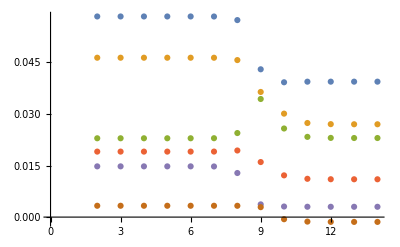

```mathematica
plotvals2=Table[
fluxnumbers=N@{n5->1000,n5h->1000,n1-> 10^n1ind};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
{n1ind,Simplify[Eigenvalues[matrixcomp/.ccval/.oneloopvalsString]][[ind]]}
,{ind,1,6},{n1ind,2,14}];
ListPlot@plotvals2
```

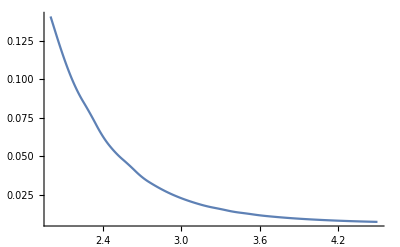

```mathematica
ListPlot[plotvals,PlotRange->All,Joined->True,InterpolationOrder->2]
```

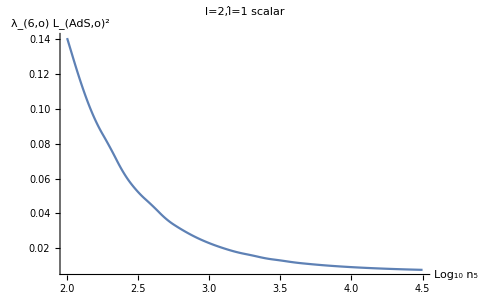

```mathematica
Show[%257,AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 5]],HoldForm[Subscript[λ, 6,o] Subscript[L, AdS,o]^2]},PlotLabel->RawBoxes[RowBox[{RowBox[{"l","=","2"}],",",RowBox[{OverscriptBox["l","^"],"=",RowBox[{"1"," ","scalar"}]}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
OverHat[l]
```

l̂

### lm=0,lp>1

```mathematica
Clear[algebraicrules,specialrule,matrix,tensorlist,matrixcomp,massessquared,lm];
specialrule=Flatten[Map[MakeRule[#]&,{{ℒ[],0},{𝒲[],0},{𝒟[],0},{𝒮[],0}}]];(*ℒ, 𝒲, 𝒟 and 𝒮 are now set to zero*)
lm=0;
```

#### Redundancies among Equations

```mathematica
algebraicrules=SolveTensors[(scalargabtraceless/.specialrule)==0,ϕs[]];
algebraicrules=Flatten[Append[algebraicrules,SolveTensors[(scalargμνtrace-4scalargabtrace/.algebraicrules/.specialrule)==0,𝒱[]][[1]]]];
```

```mathematica
CollectTensors[lp(lp+2)/2 scalargμνtrace- √(4+2 rp^2 Λ)scalarXacomp+rp^2 scalargμacomp/.specialrule/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]]
scalargijtraceless/.algebraicrules/.specialrule
(*Thus scalargμacomp and scalarijtraceless are not independent equations and we do not have to consider them any longer*)
```

0

0

#### Representing Matrix

```mathematica
tensorlist={ℳ[],𝒩[],𝒫[],𝒰[],ℋ[]};
matrix=SolveTensors[CollectTensors/@{(scalarϕcomp/.algebraicrules/.specialrule)==0,(scalargμνtrace/.algebraicrules/.specialrule)==0,(scalargijtrace/.algebraicrules/.specialrule)==0,(scalarXμcomp/.algebraicrules/.specialrule)==0,(scalarXacomp/.algebraicrules/.specialrule)==0}/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]],CDAdS3[-λ]@CDAdS3[λ]@#&/@tensorlist][[1]];
```

```mathematica
(*Check whether also the quadratic equation is satisfied*)
Simplify[scalargμνtraceless/.algebraicrules/.specialrule/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.matrix/.matrix//CollectTensors]
(*Thus all scalar equations are satisfied by this solution*)
```

0

```mathematica
(*Write rule as a matrix*)
matrixcomp=Coefficient[CDAdS3[-λ][CDAdS3[λ][#]]&/@tensorlist/.matrix,#]&/@tensorlist;
```

```mathematica
massessquared=Simplify[Eigenvalues[matrixcomp/.ccval/.oneloopvalsString/.harmonicnumbers]]
```

{0.0338885,0.024,0.016,-0.00188854,-8.39062×10^-11}

### lm>1,lp=0

```mathematica
Clear[algebraicrules,specialrule,matrix,tensorlist,matrixcomp,massessquared,lm];
specialrule=Flatten[Map[MakeRule[#]&,{{𝒱[],0},{ℋ[],0},{ϕs[],3/4 ℳ[]+1/4 𝒩[]+3/4 𝒫[]}}]];(*𝒱 is trivially zero, 3/4 ℳ+1/4 𝒩+3/4 𝒫-ϕs and ℋ are now set to zero using residual gauge transformations*)
lp=0;
lm=2;
```

#### Redundancies among Equations

```mathematica
algebraicrules=SolveTensors[(scalargμνtrace-4scalargabtrace/.specialrule)==0,𝒮[]][[1]];
```

```mathematica
CollectTensors[(2 lm(lm+2))/rm^2 scalargijtrace+scalargijtraceless+scalargμicomp-2 rm^-2 scalarXicomp/.specialrule/.algebraicrules]
(*Thus scalargμacomp and scalarijtraceless are not independent equations and we do not have to consider them any longer*)
```

#### Representing Matrix

```mathematica
tensorlist={ℳ[],𝒩[],𝒫[],𝒰[],𝒲[],ℒ[]};
matrix=SolveTensors[CollectTensors/@{(scalarϕcomp/.algebraicrules/.specialrule)==0,(scalargμνtrace/.algebraicrules/.specialrule)==0,(scalargijtrace/.algebraicrules/.specialrule)==0,(scalargμicomp/.algebraicrules/.specialrule)==0,(scalarXμcomp/.algebraicrules/.specialrule)==0,(scalarXicomp/.algebraicrules/.specialrule)==0}/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]],CDAdS3[-λ]@CDAdS3[λ]@#&/@tensorlist][[1]];
```

```mathematica
(*Check whether also the quadratic equation is satisfied*)
Simplify[scalargμνtraceless/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.algebraicrules/.specialrule/.matrix/.matrix]
(*Thus all scalar equations are satisfied by this solution*)
```

1/12 Λ ((12/rm^2+12/rp^2-9 Λ) (h | M |  
  | M)-(36 ℳ)/rm^2-(132 ℳ)/rp^2+279 Λ ℳ+(60 𝒩)/rm^2+(124 𝒩)/rp^2+167 Λ 𝒩+(156 𝒫)/rm^2-(36 𝒫)/rp^2+207 Λ 𝒫+32 𝒰-32 𝒲-4 ∇_μ ∇^μ h | M |  
  | M)

```mathematica
(*Write rule as a matrix*)
matrixcomp=Coefficient[CDAdS3[-λ][CDAdS3[λ][#]]&/@tensorlist/.matrix,#]&/@tensorlist;
```

```mathematica
massessquared=Simplify[Eigenvalues[matrixcomp/.ccval/.oneloopvalsString]]
```

{0.338885,0.24,0.16,0.06,-0.0188854,-2.65335×10^-9}

```mathematica
plotvals=Table[
fluxnumbers=N@{n5->10^n1ind,n5h->1000,n1-> 10^1};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
{n1ind,Simplify[Eigenvalues[matrixcomp/.ccval/.oneloopvalsString]][[3]]}
,{n1ind,2,4.5,0.1}];
```

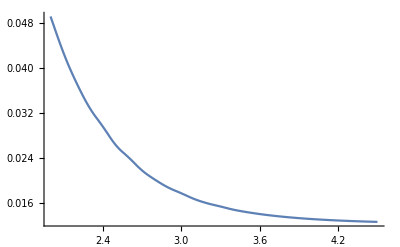

```mathematica
ListPlot[plotvals,PlotRange->All,Joined->True,InterpolationOrder->2]
```

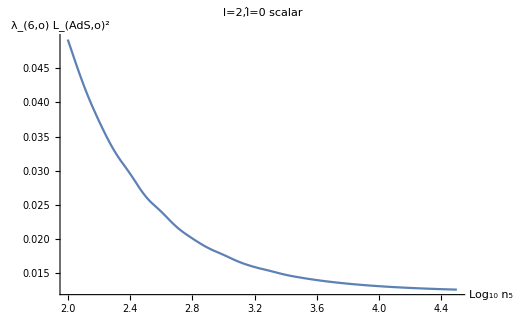

```mathematica
Show[%199,AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 5]],HoldForm[Subscript[λ, 6,o] Subscript[L, AdS,o]^2]},PlotLabel->RawBoxes[RowBox[{RowBox[{"l","=","2"}],",",RowBox[{OverscriptBox["l","^"],"=",RowBox[{"0"," ","scalar"}]}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
OverHat[l]
```

l̂

```mathematica
plotvals[[18]]
```

{3.7,0.013747}

```mathematica
nn=14;
plotvals[[nn]]=(plotvals[[nn-1]]+plotvals[[nn+1]])/2
```

{3.3,0.0153763}

```mathematica
(2 ℓ^-1-√( rm^-2(lm+1)^2+rp^-2(lp+1)^2))^2-ℓ^-2/.Λ->0/.oneloopvalsString
(2 ℓ^-1+√( rm^-2(lm+1)^2+rp^-2(lp+1)^2))^2-ℓ^-2/.Λ->0/.oneloopvalsString
```

-0.00188856

0.0338888

### lm=1,lp=0

```mathematica
Clear[algebraicrules,specialrule,matrix,tensorlist,matrixcomp,massessquared,lm];
specialrule=Flatten[Map[MakeRule[#]&,{{𝒱[],0},{ℋ[],0},{ℒ[],0},{ϕs[],3/4 ℳ[]+1/4 𝒩[]+3/4 𝒫[]}}]];(*𝒱 and ℒ are trivially zero, 3/4 ℳ+1/4 𝒩+3/4 𝒫-ϕs and ℋ are now set to zero using residual gauge transformations*)
lp=0;
lm=1;
```

#### Redundancies among Equations

```mathematica
algebraicrules=SolveTensors[(scalargμνtrace-4scalargabtrace/.specialrule)==0,𝒮[]][[1]];
```

```mathematica
CollectTensors[(2 lm(lm+2))/rm^2 scalargijtrace+scalargijtraceless+scalargμicomp-(√(4+2 rm^2 Λ))/rm^2 scalarXicomp/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]]/.rm->1
(*Thus scalargμacomp and scalarijtraceless are not independent equations and we do not have to consider them any longer*)
```

-6 𝒱

#### Representing Matrix

```mathematica
tensorlist={ℳ[],𝒩[],𝒫[],𝒰[],𝒲[]};
matrix=SolveTensors[CollectTensors/@{(scalarϕcomp/.algebraicrules/.specialrule)==0,(scalargμνtrace/.algebraicrules/.specialrule)==0,(scalargμicomp/.algebraicrules/.specialrule)==0,(scalarXμcomp/.algebraicrules/.specialrule)==0,(scalarXicomp/.algebraicrules/.specialrule)==0}/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]],CDAdS3[-λ]@CDAdS3[λ]@#&/@tensorlist][[1]];
```

```mathematica
(*Check whether also the quadratic equation is satisfied*)
Simplify[scalargμνtraceless/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.specialrule/.matrix/.matrix]
(*Thus all scalar equations are satisfied by this solution*)
```

0

```mathematica
(*Write rule as a matrix*)
matrixcomp=Coefficient[CDAdS3[-λ][CDAdS3[λ][#]]&/@tensorlist/.matrix,#]&/@tensorlist;
ccval2=Λ->0;
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
```

```mathematica
fluxnumbers=N@{n5->100,n5h->100,n1-> 10^12};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval2/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;


massessquared=Simplify[Eigenvalues[matrixcomp/.ccval2/.oneloopvalsString]]
```

{0,0,0,0,0,0}

```mathematica
plotvals=Table[
fluxnumbers=N@{n5->10^n1ind,n5h->1000,n1-> 10^1};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
{n1ind,Simplify[Eigenvalues[matrixcomp/.ccval/.oneloopvalsString]][[3]]}
,{n1ind,2,4.5,0.1}];
```

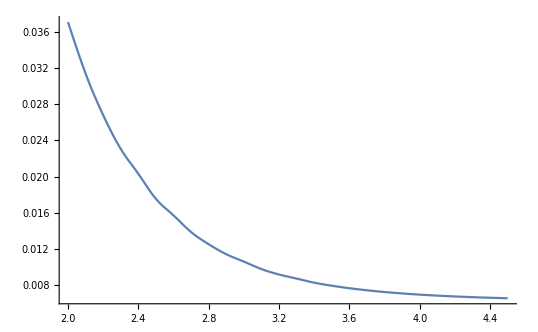

```mathematica
ListPlot[plotvals,PlotRange->All,Joined->True,InterpolationOrder->2]
```

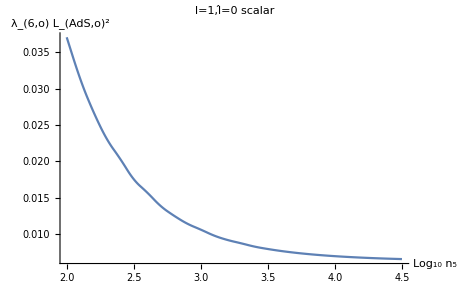

```mathematica
Show[%198,AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 5]],HoldForm[Subscript[λ, 6,o] Subscript[L, AdS,o]^2]},PlotLabel->RawBoxes[RowBox[{RowBox[{"l","=","1"}],",",RowBox[{OverscriptBox["l","^"],"=",RowBox[{"0"," ","scalar"}]}]}]],LabelStyle->{GrayLevel[0]}]
```

### lp=0, lm=0

```mathematica
Clear[algebraicrules,specialrule,matrix,tensorlist,matrixcomp,massessquared,lm];
specialrule=Flatten[Map[MakeRule[#]&,{{𝒱[],0},{𝒲[],0},{ℒ[],0},{𝒮[],0},{ϕs[],3/4 ℳ[]+1/4 𝒩[]+3/4 𝒫[]}}]];(*𝒱, 𝒲, 𝒮 and ℒ are trivially zero, 3/4 ℳ+1/4 𝒩+3/4 𝒫-ϕs is now set to zero using residual gauge transformations*)
lp=0;
lm=0;
```

#### Redundancies among Equations

```mathematica
algebraicrules=SolveTensors[(scalargμνtrace-4scalargabtrace/.specialrule)==0,𝒰[]][[1]];
```

#### Representing Matrix

```mathematica
tensorlist={ℳ[],𝒩[],𝒫[],ℋ[]};
matrix=SolveTensors[CollectTensors/@{(scalarϕcomp/.algebraicrules/.specialrule)==0,(scalargμνtrace/.algebraicrules/.specialrule)==0,(scalargijtrace/.algebraicrules/.specialrule)==0,(scalarXμcomp/.algebraicrules/.specialrule)==0}/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]],CDAdS3[-λ]@CDAdS3[λ]@#&/@tensorlist][[1]];
```

```mathematica
(*Check whether also the quadratic equation is satisfied*)
Simplify[scalargμνtraceless/.algebraicrules/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.specialrule/.Flatten[Map[MakeRule[#]&,{{ {{h, {{M, }, {, M}}}},3(ℳ+ 𝒩+ 𝒫)}}]]/.matrix/.matrix]
(*Thus all scalar equations are satisfied by this solution*)
```

0

```mathematica
(*Write rule as a matrix*)
matrixcomp=Coefficient[CDAdS3[-λ][CDAdS3[λ][#]]&/@tensorlist/.matrix,#]&/@tensorlist;
```

## Plotting the values

### Plotting the BF - saturating tachyon

```mathematica
plotvals=Table[
fluxnumbers=N@{n5->1000,n5h->1000,n1-> 10^n1ind};
harmonicnumbers={lp->1,lm->1};
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
massessquared=Simplify[Eigenvalues[matrixcomp ℓ^2/.harmonicnumbers/.ccval/.oneloopvalsString]][[ind]],{ind,1,7},{n1ind,4,16,1/4}];
```

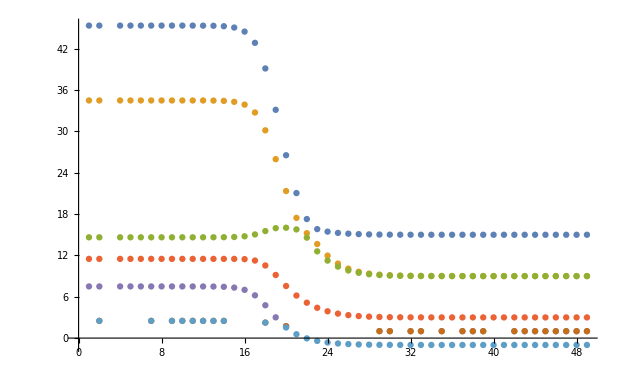

```mathematica
ListPlot@plotvals
```

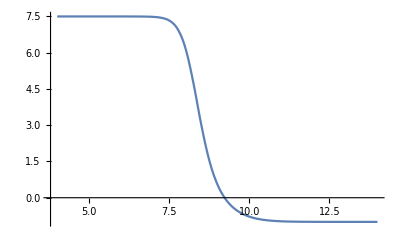

```mathematica
tachyonvals=Join[plotvals[[5,1;;2]],{plotvals[[5,2]]+plotvals[[5,4]]}/2,plotvals[[5,4;;19]],plotvals[[7,20;;41]]];
tachyonplot=ListPlot[Table[{4+(n1ind-1)/4,tachyonvals[[n1ind]]},{n1ind,1,41}],Joined->True,InterpolationOrder->2]
```

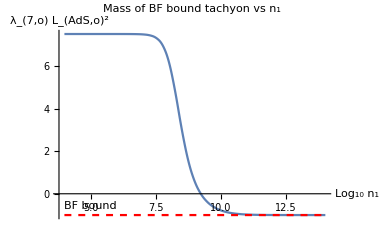

```mathematica
Show[{tachyonplot,Plot[-1,{x,4,14},PlotStyle->Directive[Red,Dashed],PlotLabels->Placed["BF bound",{5,-0.9}]]},AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 1]],HoldForm[Subscript[λ, 7,o] Subscript[L, AdS,o]^2]},PlotLabel->HoldForm[Mass of BF bound tachyon vs Subscript[n, 1]],LabelStyle->{GrayLevel[0]}]
```

### Plotting the scalars

```mathematica
l00mass={};
```

```mathematica
plotvals=Table[
fluxnumbers=N@{n5->10^n5ind,n5h->1000,n1-> 1};
harmonicnumbers={lp->0.001,lm->0.001};
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
massessquared=Simplify[Eigenvalues[matrixcomp ℓ^2/.harmonicnumbers/.ccval/.oneloopvalsString]][[ind]],{ind,{3}},{n5ind,0,9,1/4}];
```

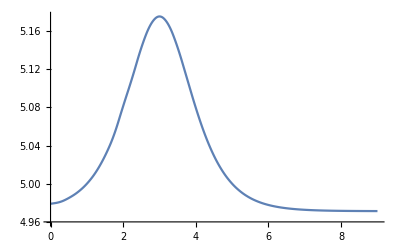

```mathematica
ListPlot[Table[{(ind-1)/4,plotvals[[1,ind]]},{ind,1,37}],Joined->True,InterpolationOrder->2]
```

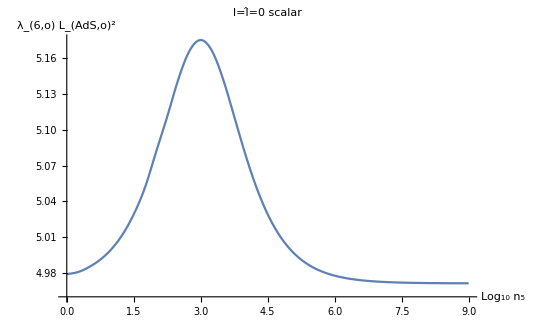

```mathematica
Show[%123,AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 5]],HoldForm[Subscript[λ, 6,o] Subscript[L, AdS,o]^2]},PlotLabel->HoldForm[l=l̂=0 scalar],LabelStyle->{GrayLevel[0]}]
```

```mathematica
l00mass={};
plotvals=Table[
fluxnumbers=N@{n5->10^n5ind,n5h->1000,n1-> 1};
harmonicnumbers={lp->2,lm->0.001};
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
massessquared=Simplify[Eigenvalues[matrixcomp ℓ^2/.harmonicnumbers/.ccval/.oneloopvalsString]][[ind]],{ind,{7}},{n5ind,0,9,1/4}];
```

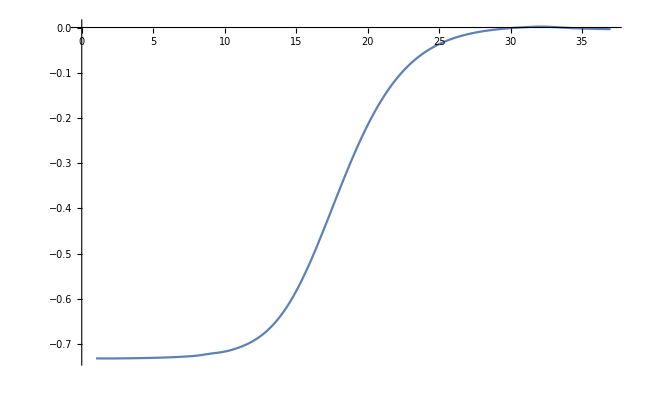

```mathematica
ListPlot[plotvals,Joined->True,InterpolationOrder->2]
```

```mathematica
l20mass={};
plotvals2=Table[
fluxnumbers=N@{n5->10^n5ind-0.1,n5h->1000,n1-> 1};
harmonicnumbers={lp->2,lm->0.001};
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
massessquared=Simplify[Eigenvalues[matrixcomp ℓ^2/.harmonicnumbers/.ccval/.oneloopvalsString]][[ind]],{ind,{7}},{n5ind,0,9,1/4}];
```

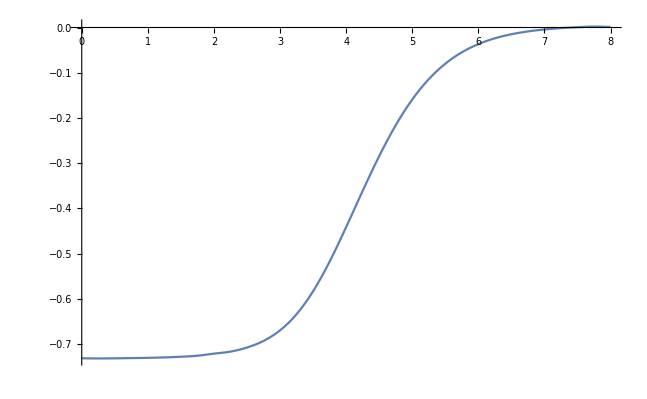

```mathematica
ListPlot[Table[{(ind-1)/4,plotvals2[[1,ind]]},{ind,1,33}],Joined->True,InterpolationOrder->2]
```

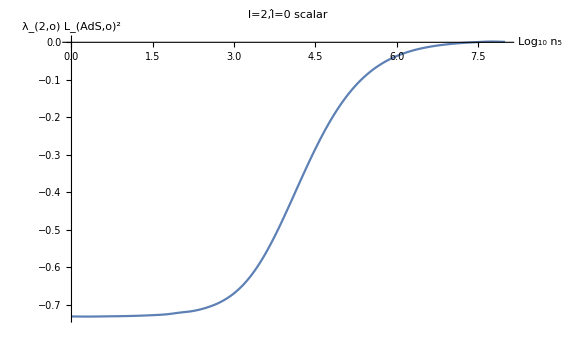

```mathematica
Show[%266,AxesLabel->{HoldForm[Subscript[Log, 10] Subscript[n, 5]],HoldForm[Subscript[λ, 2,o] Subscript[L, AdS,o]^2]},PlotLabel->RawBoxes[RowBox[{RowBox[{"l","=","2"}],",",RowBox[{OverscriptBox["l","^"],"=",RowBox[{"0"," ","scalar"}]}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
l20mass={};
plotvals2=Table[
fluxnumbers=N@{n5->10^3,n5h->1000,n1-> 10^n5ind};
harmonicnumbers={lp->1,lm->0.001};
ccval={Λ-> 0.000022991174271160088*(2π)^6/2 go^2};
oneloopvalsString=NSolve[{4n5^2/rp^6-4/rp^2-2Λ==0,4n5h^2/rm^6-4/rm^2-2Λ==0,64π^2go^4 n1^2/(rp rm)^6 -4 ℓ^-2+2Λ==0}/.ccval/.fluxnumbers,{go,rp,rm},PositiveReals][[-1]]//Reverse;
massessquared=Simplify[Eigenvalues[matrixcomp ℓ^2/.harmonicnumbers/.ccval/.oneloopvalsString]][[ind]],{ind,{7}},{n5ind,0,9,1/4}];
```

# Intrinsically quantum solution

We set n_1=0 before we solve for the minimum of the potential.

```mathematica
qgradcomp1=1/4 ( D[#,ϕ]+D[#,χ])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0,n1->0}//Expand//Simplify
qgradcomp2=1/4 (D[#,ϕ]+ D[#,χh])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0,n1->0}//Expand//Simplify
qgradcomp3=1/4 (2D[#,ϕ]+D[#,χ])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0,n1->0}//Expand//Simplify
```

3/Lho^2+6/Lo^2-(4 n5^2 α^2)/Lo^6-(n5h^2 α^2)/Lho^6

6/Lho^2+3/Lo^2-(n5^2 α^2)/Lo^6-(4 n5h^2 α^2)/Lho^6

-3/Lho^2-(2 n5^2 α^2)/Lo^6+(n5h^2 α^2)/Lho^6+(3 go^2 λ)/α

```mathematica
Solve[{qgradcomp1==0,qgradcomp2==0,qgradcomp3==0},{Lo,Lho,go}]
```

{{Lo→-((7 n5^2 α^2)/36+1-1-1/2 √(-245/9 n5^2 n5h^2 α^4+(49 1)/2592-1/1-5/18 1-(350/3 n5^4 n5h^2 α^6-1715/108 n5^2 n5h^2 α^4 (4 n5^2 α^2+49 n5h^2 α^2)+(343 1^3)/46656)/(4 √((49 n5^4 α^4)/324-6419/648 n5^2 n5h^2 α^4+1/5184+1/(18 1)+5/18 (1)^(1/3)))))^(1/4),Lho→-(√1)/(10 √2 n5^3 α^3),go→-(√(9450 n5^4 n5h^2 α^6 √((7 n5^2 α^2)/36+(343 n5h^2 α^2)/144-1/2 √1-1/2 √(-245/9 n5^2 n5h^2 α^4+7))+7))/(25 n5^3 n5h α^(7/2) √λ)},62,{Lo→((7 n5^2 α^2)/36+1/144+1+1/2 √1)^(1/4),Lho→(√1)/1,go→(√(1+7))/(25 n5^3 n5h α^1 √λ)}}
 |  |  |  |

The expressions for L_o,(L̂)_o,g_(s,o) are too complicated. So we let n_5=(n̂)_5=n and solve for the minimum of the potential again. We also use the fact that L_o=(L̂)_o by symmetry.

```mathematica
qgradcompsimple1=1/4 ( D[#,ϕ]+D[#,χ])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0,n1->0,n5->n,n5h->n,Lho->Lo}//Expand//Simplify
qgradcompsimple2=1/4 (2D[#,ϕ]+D[#,χ])&[onelooppotential[ϕ,σ,χ,χh]]/.{ϕ->0,σ->0,χ->0,χh->0,n1->0,n5->n,n5h->n,Lho->Lo}//Expand//Simplify
```

(9 Lo^4-5 n^2 α^2)/Lo^6

-3/Lo^2-(n^2 α^2)/Lo^6+(3 go^2 λ)/α

```mathematica
Solve[{qgradcompsimple1==0,qgradcompsimple2==0},{Lo,go}]
```

{{Lo→-(5^(1/4) √n √α)/(√3),go→-(2 √6)/(5^(3/4) √n √λ)},{Lo→-(5^(1/4) √n √α)/(√3),go→(2 √6)/(5^(3/4) √n √λ)},{Lo→-(ⅈ 5^(1/4) √n √α)/(√3),go→-(2 ⅈ √6)/(5^(3/4) √n √λ)},{Lo→-(ⅈ 5^(1/4) √n √α)/(√3),go→(2 ⅈ √6)/(5^(3/4) √n √λ)},{Lo→(ⅈ 5^(1/4) √n √α)/(√3),go→-(2 ⅈ √6)/(5^(3/4) √n √λ)},{Lo→(ⅈ 5^(1/4) √n √α)/(√3),go→(2 ⅈ √6)/(5^(3/4) √n √λ)},{Lo→(5^(1/4) √n √α)/(√3),go→-(2 √6)/(5^(3/4) √n √λ)},{Lo→(5^(1/4) √n √α)/(√3),go→(2 √6)/(5^(3/4) √n √λ)}}

We choose the real positive roots:

```mathematica
{Lo^2,go^2}/.{Lo->(5^(1/4) √n √α)/(√3),go->(2 √6)/(5^(3/4) √n √λ)}
```

{1/3 √5 n α,24/(5 √5 n λ)}